# Data Science and Machine Learning

## Lab session 03: Data acquisition and structure

## Entities

### What is an entity?

Entities are WL objects that provide detailed, curated, computed data about a given concept or notion, characterized by their types. They are hundreds of entity types that represent physical entities as well as mathematical and other scientific concepts.

Entities can be accessed via natural language input or programmatically retrieved and incorporated into complex computations.
To access entity via natural language input, simply use: Insert → Inline Free-Form Input

```mathematica
LinguisticAssistant (* Type your search inside the box, then press enter *)
```

```mathematica
LinguisticAssistant
```

Wolfram Language will interpret your entry. You can accept the interpretation or select an alternative one (thee dots).

```mathematica
Entity["Species","Species:UnciaUncia"]
```

snow leopard

To retrieve the Wolfram Language input form of your search, you can use InputForm

```mathematica
InputForm[Entity["Species","Species:UnciaUncia"]]
```

"Entity[\"Species\", \"Species:UnciaUncia\"]"

```mathematica
Entity["Country", "Switzerland"]
```

Switzerland

You can find the list of entities of a given type using EntityList.

```mathematica
EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

### Entity class

Entities can be grouped in class:

```mathematica
EntityClass["Country","GermanSpeaking"] (* The dots on the left indicate that the result is a list of entities *)
```

```mathematica
EntityList[EntityClass["Country","GermanSpeaking"]]
```

{Austria,Belgium,Germany,Italy,Liechtenstein,Luxembourg,Namibia,Switzerland}

You can use EntityClass to find all entities of a given class:

```mathematica
EntityClass["Country", "Europe"]
```

Europe

```mathematica
EntityList[EntityClass["Country","Europe"]]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,North Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

### Entity properties

Entities have properties that classified the data available for a given entity type.

```mathematica
EntityProperties["Species"]
```

{alternate common names,alternate scientific names,body temperature,class,common name,entity classes,family,genus,image,infraspecies,kingdom,length,maximum recorded lifespan,maximum speed,name,number of child taxa,order,parent taxon,phylum,scientific name,sibling taxa,species,reference,child taxa,taxonomic level,taxonomic sequence,taxonomy graph,weight}

Alternatively:

```mathematica
Entity["Country", "Switzerland"]["Properties"]
```

{adjusted net national income,seasonal bank borrowings from Fed, plus adjustments,regions,adult population,obese adults,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,aggregate weekly hours index,agricultural irrigated land fraction,agricultural land fraction,agricultural production index,agricultural production per capita index,agricultural products,consumption,consumption per capita,harvest area,harvest area per capita,production,production per capita,average yield,yield per capita,arrivals by air,aircraft carriers,air force,airports,air transport,alcohol fuel,total primary energy,alternate names,AM radio stations,annual annulments,annual births,annual deaths,annual divorces,annual HIV/AIDS deaths,annual marriages,antenatal care coverage,annual-crop land area,annual-crop land fraction,total area,armored infantry fighting vehicles,armored personnel carriers,army,artillery,attack helicopters,automobile production,average hourly earnings,average length of stay,average number of meetings with tax officials,average time to clear exports through customs,average weekly hours,average weekly overtime hours,aviation gasoline,bankers acceptance rate,bank prime loan rate,bank prime loan rate changes,benefits cost index,birth rate fraction,births attended by skilled health personnel,births by caesarean section,book titles published,bordering countries/regions,shared border lengths,full boundary length,burden of customs procedure,number of burglaries,rate of burglary,business activity index,professional arrivals,business entry rate,business extent of disclosure,calling code,capacity utilization rate,capital city,capital location,S&P/Case-Shiller home price index,central bank intervention,certificate of deposit,changes in inventories,checkable deposits,chemicals fraction of manufacturing value added,child employment,child population,vitamin A supplementation,children not enrolled in schools,overweight children,antimalarial treatment for fever,stunted children,underweight children,children with ARI symptoms taken to facility,diarrheal treatment with ORT,children sleeping under insecticide-treated nets,cinema attendance,number of cinemas,cinema seats,civilian employment population ratio,civilian labor force,civilian participation rate,civilian unemployment rate,classes,climate types,lignite brown coal,coal,coal,coast guard,coastline length,commercial banks assets,commercial banks credit,commercial paper,commercial paper of nonfinancial companies,community and traditional health workers,community and traditional health workers per capita,compensation per hour index,school completion rate,prevalence of condom use by young people,construction value added,consumer credit,consumer price index,consumer sentiment,container port traffic,continent,contraceptive prevalence,contributing family workers,contributing family workers fraction,conventional mortgage rate,corporate bond yield,corporate capital consumption adjustment,corporate cash flow,corporate dividends,corporate inventory valuation adjustment,corporate profits,corporate proprietors income,475,people injured in road accidents per population,people killed in road accidents,people killed in road accidents per amount of traffic,people killed in road accidents per population,arrivals by road,highways density,length of highways,motorways density,length of motorways,other roads density,length of other road types,total road density,secondary roads density,length of secondary roads,total road length,road transport,road sector diesel fuel consumption,road sector energy consumption,road sector energy consumption fraction,road sector gasoline fuel consumption,bus traffic,motorcycle traffic,passenger car traffic,total road traffic,truck and van traffic,number of robberies,rate of robbery,roundwood production,saving,savings deposits,savings and small time deposits,sawnwood production,schematic polygon,school enrollment fraction,seasonal bank borrowings from Fed,sector labor fractions,secure internet servers,securities lent to dealers,self employed,self employed fraction,service related deposits,shape,share of women employed,short wave radio stations,signed environmental agreements,spot oil price,school starting age,start up procedures to register a business,statistical discrepancy,strength of legal rights,submarines,suffrage type,target federal funds rate,number of business taxes,telephone lines,television receivers,television stations,terms of trade adjustment,terrain types,terrestrial protected areas,textiles and clothing fraction of manufacturing value added,time deposits,typical time required to build a warehouse,typical time required to enforce a contract,typical time required to obtain an operating license,typical time required to register property,typical time required to start a business,total time and savings deposits,time to prepare and pay taxes,time to resolve insolvency,time zones,current tobacco use among adolescents,current tobacco use among adults,total annual visitors,total borrowings,total registered businesses,total business inventory,total business tax rate,total fertility rate,trade value,trade balance,trade deficit,trade value added,trade-weighted exchange index,transportation value added,traveler's checks outstanding,treasury security,treasury average yield,treasury deposits,treasury securities composite rate,UN code,unemployed people,unemployment average duration,unemployment median duration,unemployment rate,unilateral current transfers,unit labor cost,unit nonlabor cost,UN number,unpaved airport lengths,unpaved airports,unpaved road length,unweighted sample housing units,unweighted sample population,uranium,change in US owned assets abroad,GDP value added,losses due to electrical outages,vault cash,vehicle sales,buses in use,buses in use per road length,buses in use per population,motorcycles in use,motorcycles in use per road length,motorcycles in use per population,passenger cars in use,passenger cars in use per road length,passenger cars in use per population,total vehicles in use,total vehicles in use per road length,total vehicles in use per population,trucks and vans in use,trucks and vans in use per road length,trucks and vans in use per population,total rate of violent crime,total number of violent crimes,vulnerable employment,vulnerable employment fraction,wage and salaried workers,wage and salaried workers fraction,wage cost index,water area,arrivals by sea,water productivity,waterway length,employment,wholesale price index}
 |  |  |  |

### Working with entity

You can use EntityValue to access the value(s) of a specified property for a given entity:

```mathematica
EntityValue[Entity["Species","Species:UnciaUncia"], "Image"]
```

-Graphics-

Alternatively, you can use functions specific to a given entity type such as: SpeciesData, PlantData, CountryData, CityData, FinancialData,

You can extract several properties at the same time:

```mathematica
SpeciesData[Entity["Species","Species:UnciaUncia"],{"Weight", "Family"}]
```

{(800.to2800.) oz,cats}

You can also extract the value of a given property for several entities of the same type:

```mathematica
EntityValue[{Entity["Country","Switzerland"],Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]}, "GDP"]
```

{7.03082×10^11 $,2.71552×10^12 $,3.86112×10^12 $,2.00358×10^12 $}

Another way to obtain the same result, using Map:

```mathematica
CountryData[#,"GDP"]& /@ {Entity["Country","Switzerland"],Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]} (* Note that EntityValue works with a class or list of entities as first argument, but CountryData does not, and thus requires a Map *)
```

{7.03082×10^11 $,2.71552×10^12 $,3.84563×10^12 $,2.00124×10^12 $}

You can use the values of entities to perform calculation and generate plots.

For instance, we sort the European countries area from largest to smallest:

```mathematica
countryArea={CountryData[#, "Area"],#}&/@ CountryData[EntityClass["Country","Europe"]]; (* We create a list of {Country Area, Country Entity}. Note the use of pure function and Map (f /@ list). *)
Last /@ Reverse @ Sort[countryArea]    (* We Sort the list from smallest area to largest, Reverse it, and then use Last to select the second (last) element of each list, i.e. the country entities *)
```

{Ukraine,France,Spain,Sweden,Germany,Finland,Norway,Poland,Italy,United Kingdom,Romania,Belarus,Greece,Bulgaria,Iceland,Hungary,Portugal,Austria,Czech Republic,Serbia,Ireland,Lithuania,Latvia,Svalbard,Croatia,Bosnia and Herzegovina,Slovakia,Estonia,Denmark,Netherlands,Switzerland,Moldova,Belgium,Albania,North Macedonia,Slovenia,Montenegro,Kosovo,Cyprus,Luxembourg,Faroe Islands,Isle of Man,Andorra,Malta,Liechtenstein,Jersey,Guernsey,San Marino,Gibraltar,Monaco,Vatican City}

Here is the evolution of GDP per capita in Switzerland.
DateListPlot allows to plot time series.

```mathematica
gdpCapitaCH = CountryData[Entity["Country","Switzerland"],{{"GDP"},{1960,2019}}]/CountryData[Entity["Country","Switzerland"],{{"Population"},{1960,2019}}]; (* GDP per capita in Switzerland between 1960 and 2019 *)
DateListPlot[gdpCapitaCH]
```

-Graphics-

You can plot several time series on the same graph. 
For instance, here is the evolution of GDP per capita in some European countries

```mathematica
gdpCapita[country_] := #2[#1,{{"GDP"},#3}]/#2[#1,{{"Population"},#3}] &[country,CountryData, {1960,2019}]; 
(* Here we defined a function gdpCapita that computes the GDP per capita for a given country. 
Note the use of pure function inside our defined function to simply the expression: no need to repeat the country, the function CountryData, and the timeframe *)
DateListPlot[{gdpCapita[#1],gdpCapita[#2], gdpCapita[#3], gdpCapita[#4]}, PlotLegends ->{#1,#2, #3, #4}] &[Entity["Country","Switzerland"], Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]]
```

-Graphics-

Here is a geographic plot of the literacy rate in African countries. It is using the entity class "Africa" and the function GeoRegionValuePlot:

```mathematica
GeoRegionValuePlot[EntityClass["Country","Africa"]->"LiteracyRate"]
```

-Graphics-

### Structuring your data from entities

You can create Associations and Dataset directly using EntityValue

```mathematica
EntityValue[{Entity["Country","Switzerland"],Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]}, {"GDP","Population"}, "PropertyAssociation"]
EntityValue[{Entity["Country","Switzerland"],Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]}, {"GDP","Population"}, "EntityAssociation"]
EntityValue[{Entity["Country","Switzerland"],Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]}, {"GDP","Population"}, "EntityPropertyAssociation"]
EntityValue[{Entity["Country","Switzerland"],Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"]}, {"GDP","Population"}, "Dataset"]
```

{<|GDP→7.03082×10^11 $,Population→8654618 people|>,<|GDP→2.71552×10^12 $,Population→65273512 people|>,<|GDP→3.86112×10^12 $,Population→83783945 people|>,<|GDP→2.00358×10^12 $,Population→60461828 people|>}

<|Switzerland→{7.03082×10^11 $,8654618 people},France→{2.71552×10^12 $,65273512 people},Germany→{3.86112×10^12 $,83783945 people},Italy→{2.00358×10^12 $,60461828 people}|>

<|Switzerland→<|GDP→7.03082×10^11 $,Population→8654618 people|>,France→<|GDP→2.71552×10^12 $,Population→65273512 people|>,Germany→<|GDP→3.86112×10^12 $,Population→83783945 people|>,Italy→<|GDP→2.00358×10^12 $,Population→60461828 people|>|>

## Wolfram Data Repository

The Wolfram Data Repository is a public resource that hosts a collection of computable datasets, curated and structured to be suitable for immediate use in computation, visualization, analysis and more.

ResourceObject allows to represent a resource with the given name. ResourceData allows to import the content.
For instance, let's import "The Big Mac Index" data repository.

```mathematica
ResourceObject["The Big Mac Index"]
```

ResourceObject[…]

```mathematica
bigmac=ResourceData["The Big Mac Index"]
```

Use Head to obtain the head of a given expression. It allows to identify the type of the object.

```mathematica
bigmac // Head
```

Dataset

The object "bigmac" is a Dataset (see Help notebook on dataset). You can perform operations and plot some elements of this dataset.

For instance, if we want to extract the evolution of big mac dollar prices for Argentina (second row)

```mathematica
bigmac[[2,"DollarPrice"]]
```

TimeSeries[…]

Alternatively, using Select:

```mathematica
dolpriceARG =bigmac[
   Select[#Country ===Entity["Country","Argentina"] &]][All,  "DollarPrice"]
```

Note that this formulation gives a Dataset while the previous one extracted a TimeSeries

```mathematica
Head[dolpriceARG]
```

Dataset

We can compute the average price of Big Mac in Argentina between 2000 and 2018 (in dollar):

```mathematica
dolpriceARG [TimeSeries] //Mean       (* We first convert our dataset into a time series before applying Mean *)
```

2.93 $

We can plot this timeseries:

```mathematica
DateListPlot[dolpriceARG, PlotLegends ->"Dollar Price", PlotLabel -> Entity["Country","Argentina"] , Filling -> Bottom ]
```

-Graphics-

## Import Data

You can use Import to import data from a variety of sources. Here are the possible formats (see also a description here):

```mathematica
$ImportFormats
```

{3DS,7z,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,CDF,CDX,CDXML,Character16,Character32,Character8,CIF,CML,Complex128,Complex256,Complex64,CSV,Cube,CUR,DAE,DBF,DICOM,DICOMDIR,DIF,DIMACS,Directory,DOT,DTA,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FBX,FCHK,FCS,FITS,FLAC,GaussianLog,GenBank,GeoJSON,GeoTIFF,GIF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,ISO,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LaTeX,LEDA,List,LWO,MAT,MathML,Matroska,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOL,MOL2,MP3,MP4,MPS,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,ODS,OFF,Ogg,ONNX,OpenEXR,OWLFunctional,Pajek,PBM,PCAP,PCX,PDB,PDF,PEM,PGM,PHPIni,PLY,PNG,PNM,POR,PPM,PXR,PythonExpression,QuickTime,RAR,Raw,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SAS7BDAT,SAV,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,VCS,VideoFormat,VTK,WARC,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZSTD}

### Import from Local File

We will import the CSV file "GHG_EU.csv". It contains the GHG emissions of European countries and was obtained from Eurostat. 
Dataset: ENV_AIR_GGE
Unit: Thousand tonnes of CO2 equivalent
Source sectors for greenhouse gas emissions (Common reporting format, UNFCCC): Total (excluding memo items, including international transport)

```mathematica
ghg = Import["MGT-492/data/GHG_EU.csv", "Dataset", "HeaderLines" -> 1]
```

Extract the GHG emissions of Switzerland from 1990:

```mathematica
ghgCH = ghg[Select[#Country == "Switzerland" &], 7;;]
```

```mathematica
DateListPlot[ghgCH, PlotLabel -> "Evolution of GHG emission in Switzerland"]
```

-Graphics-

Compute the sum of emissions in Europe (from 1990):

```mathematica
ghgEU = ghg[Total,7;;]
```

```mathematica
DateListPlot[ghgEU,  PlotLabel -> "Evolution of GHG emission in Europe"]
```

-Graphics-

### Import from webpage

You can import the entire webpage:

```mathematica
sdgWiki = Import["https://en.wikipedia.org/wiki/Sustainable_Development_Goals"]
```

Sustainable Development Goals  
 
From Wikipedia, the free encyclopedia  
 
 
  Jump to navigation   Jump to search  

Set of 17 global development goals defined by the United Nations for the year 2030  
"SDG" redirects here. For other uses, see SDG (disambiguation) .  
   
Sustainable Development Goals

Mission statement "A blueprint to achieve a better and more sustainable future for all people and the world by 2030"
Type of project Non-Profit
Location Global
Owner Supported by United Nation & Owned by community
Founder United Nations
Established 2016
Website sdgs .un .org  
The Sustainable Development Goals ( SDGs ) or Global Goals are a collection of 17 interlinked global goals designed to be a "blueprint to achieve a better and more sustainable future for all". [1] The SDGs were set up in 2015 by the United Nations General Assembly and are intended to be achieved by the year 2030. They are included in a UN Resolution called the 2030 Agenda or what is colloquially known as Agenda 2030 . [2] The SDGs were developed in the Post-2015 Development Agenda as the future global development framework to succeed the Millennium Development Goals which ended in 2015. 
The 17 SDGs are: (1) No Poverty , (2) Zero Hunger , (3) Good Health and Well-being , (4) Quality Education , (5) Gender Equality , (6) Clean Water and Sanitation , (7) Affordable and Clean Energy , (8) Decent Work and Economic Growth , (9) Industry, Innovation and Infrastructure , (10) Reducing Inequality , (11) Sustainable Cities and Communities , (12) Responsible Consumption and Production , (13) Climate Action , (14) Life Below Water , (15) Life On Land , (16) Peace, Justice, and Strong Institutions , (17) Partnerships for the Goals . 
Though the goals are broad and interdependent, two years later (6 July 2017) the SDGs were made more "actionable" by a UN Resolution adopted by the General Assembly. The resolution identifies specific targets for each goal, along with indicators that are being used to measure progress toward each target. [3] The year by which the target is meant to be achieved is usually between 2020 and 2030. [4] For some of the targets, no end date is given. 
To facilitate monitoring, a variety of tools exist to track and visualize progress towards the goals. All intention is to make data more available and easily understood. [5] For example, the online publication SDG-Tracker, launched in June 2018, presents available data across all indicators. [5] The SDGs pay attention to multiple cross-cutting issues, like gender equity, education, and culture cut across all of the SDGs. There were serious impacts and implications of the COVID-19 pandemic on all 17 SDGs in the year 2020. [6]    

Contents  
1 Overview  
1.1 Ratification 1.2 Targets and indicators 1.3 Reviews of indicators 1.4 The 17 individual goals  
1.4.1 Goal 1: No poverty 1.4.2 Goal 2: Zero hunger (No hunger) 1.4.3 Goal 3: Good health and well-being 1.4.4 Goal 4: Quality education 1.4.5 Goal 5: Gender equality 1.4.6 Goal 6: Clean water and sanitation 1.4.7 Goal 7: Affordable and clean energy 1.4.8 Goal 8: Decent work and economic growth 1.4.9 Goal 9: Industry, Innovation and Infrastructure 1.4.10 Goal 10: Reduced inequality 1.4.11 Goal 11: Sustainable cities and communities 1.4.12 Goal 12: Responsible consumption and production 1.4.13 Goal 13: Climate action 1.4.14 Goal 14: Life below water 1.4.15 Goal 15: Life on land 1.4.16 Goal 16: Peace, justice and strong institutions 1.4.17 Goal 17: Partnership for the goals   1.5 Monitoring   2 Cross-cutting issues  
2.1 Gender equality 2.2 Education 2.3 Culture 2.4 Health   3 Implementation and support  
3.1 Allocation 3.2 Challenges  
3.2.1 Impacts of COVID-19 pandemic     4 Costs and sources of finance  
4.1 Costs 4.2 Financing 4.3 SDG-driven investment   5 Communication and advocacy  
5.1 Advocates 5.2 Events  
5.2.1 Global Goals Week 5.2.2 Film festivals     6 History 7 Reception  
7.1 Competing and too many goals 7.2 Weak on environmental sustainability 7.3 Importance of technology and connectivity   8 Country examples  
8.1 Asia and Pacific  
8.1.1 Australia 8.1.2 Bangladesh 8.1.3 Bhutan 8.1.4 India   8.2 Africa  
8.2.1 Nigeria 8.2.2 Ghana   8.3 Europe and Middle East  
8.3.1 Iran 8.3.2 Lebanon 8.3.3 United Kingdom   8.4 Americas  
8.4.1 United States     9 See also 10 Notes 11 References 12 Sources 13 External links       Overview [ edit ]   Ratification [ edit ]  

 

Transforming our world: the 2030 Agenda for Sustainable Development (UN Resolution A/RES/70/1), containing the goals (October 2015)  
Negotiations on the Post-2015 Development Agenda began in January 2015 and ended in August 2015. The negotiations ran in parallel to United Nations negotiations on financing for development, which determined the financial means of implementing the Post-2015 Development Agenda ; those negotiations resulted in adoption of the Addis Ababa Action Agenda in July 2015. A final document was adopted at the UN Sustainable Development Summit in September 2015 in New York . [7]  
On 25 September 2015, the 193 countries of the UN General Assembly adopted the 2030 Development Agenda titled "Transforming our world: the 2030 Agenda for Sustainable Development". [8] [9] This agenda has 92 paragraphs. Paragraph 59 outlines the 17 Sustainable Development Goals and the associated 169 targets and 232 indicators.    Targets and indicators [ edit ]  

 

Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development containing the targets and indicators, July 2017 (UN resolution A/RES/71/313)  
The lists of targets and indicators for each of the 17 SDGs was published in a UN resolution in July 2017. [3] Each goal typically has 8–12 targets, and each target has between 1 and 4 indicators used to measure progress toward reaching the targets. The targets are either "outcome" targets (circumstances to be attained) or "means of implementation" targets. [10] The latter targets were introduced late in the process of negotiating the SDGs to address the concern of some Member States about how the SDGs were to be achieved. Goal 17 is wholly about how the SDGs will be achieved. [10]  
The numbering system of targets is as follows: "Outcome targets" use numbers, whereas "means of implementation targets" use lower case letters. [10] For example, SDG 6 has a total of 8 targets. The first six are outcome targets and are labeled Targets 6.1 to 6.6. The final two targets are "means of implementation targets" and are labeled as Targets 6.a and 6.b.    Reviews of indicators [ edit ]  
As planned, the indicator framework was comprehensively reviewed at the 51st session of the United Nations Statistical Commission in 2020. It will be reviewed again in 2025. [11] At the 51st session of the Statistical Commission (held in New York City from 3–6 March 2020) a total of 36 changes to the global indicator framework were proposed for the Commission's consideration. Some indicators were replaced, revised or deleted. [11] Between 15 October 2018 and 17 April 2020, other changes were made to the indicators. [12] Yet their measurement continues to be fraught with difficulties. [13]  
The United Nations Statistics Division (UNSD) website provides a current official indicator list which includes all updates until the 51st session Statistical Commission in March 2020. [4]  
The indicators were classified into three tiers based on their level of methodological development and the availability of data at the global level. [14] Tier 1 and Tier 2 are indicators that are conceptually clear, have an internationally established methodology , and data are regularly produced by at least some countries. Tier 3 indicators had no internationally established methodology or standards. The global indicator framework was adjusted so that Tier 3 indicators were either abandoned, replaced or refined. [14] As of 17 July 2020, there were 231 unique indicators. [14]     The 17 individual goals [ edit ]  
Further information: List of Sustainable Development Goal targets and indicators   Goal 1: No poverty [ edit ]  

 

Homeless man living on the streets of Tokyo, 2008  
Main article: Sustainable Development Goal 1  
SDG 1 is to: "End poverty in all its forms everywhere". [15] Achieving SDG 1 would end extreme poverty globally by 2030.  

This section is an excerpt from Sustainable Development Goal 1 . [ edit ]
 
The goal has seven targets and 13 indicators to measure progress. The five "outcome targets" are: eradication of extreme poverty; reduction of all poverty by half; implementation of social protection systems; ensuring equal rights to ownership, basic services, technology and economic resources; and the building of resilience to environmental, economic and social disasters . The two targets related to "means of achieving" SDG 1 are mobilization of resources to end poverty; and the establishment of poverty eradication policy frameworks at all levels. [16] [17]    Despite the ongoing progress, 10 percent of the world's population live in poverty and struggle to meet basic needs such as health , education , and access to water and sanitation . [18] Extreme poverty remains prevalent in low-income countries particularly those affected by conflict and political upheaval . [19] In 2015, more than half of the world's 736 million people living in extreme poverty lived in Sub-Saharan Africa. Without a significant shift in social policy, extreme poverty will dramatically increase by 2030. [20] The rural poverty rate stands at 17.2 percent and 5.3 percent in urban areas (in 2016). [21] Nearly half are children. [21] 
A study published in September 2020 found that poverty increased by 7 per cent in just a few months due to the COVID-19 pandemic , even though it had been steadily decreasing for the last 20 years. [22] :9     Goal 2: Zero hunger (No hunger) [ edit ]  
Main article: Sustainable Development Goal 2  

 

Sufficient and healthy foods should be made available to everyone  
SDG 2 is to: "End hunger , achieve food security and improved nutrition, and promote sustainable agriculture ". [23]   

This section is an excerpt from Sustainable Development Goal 2 . [ edit ]
 SDG 2 has eight targets and 14 indicators to measure progress. [24] The five "outcome targets" are: ending hunger and improving access to food; ending all forms of malnutrition ; agricultural productivity ; sustainable food production systems and resilient agricultural practices; and genetic diversity of seeds, cultivated plants and farmed and domesticated animals; investments, research and technology. The three "means of achieving" targets include: addressing trade restrictions and distortions in world agricultural markets and food commodity markets and their derivatives. [24] 
Globally, 1 in 9 people are undernourished, the vast majority of whom live in developing countries. Under nutrition causes wasting or severe wasting of 52 million children worldwide. [25] It contributes to nearly half (45%) of deaths in children under five – 3.1 million children per year. [26]     Goal 3: Good health and well-being [ edit ]  
Main article: Sustainable Development Goal 3  

 

Mothers with healthy children in rural India  
SDG 3 is to: "Ensure healthy lives and promote well-being for all at all ages". [27]    

This section is an excerpt from Sustainable Development Goal 3 . [ edit ]
 SDG 3 has 13 targets and 28 indicators to measure progress toward targets. The first nine targets are "outcome targets". Those are: reduction of maternal mortality ; ending all preventable deaths under five years of age ; fight communicable diseases ; ensure reduction of mortality from non-communicable diseases and promote mental health ; prevent and treat substance abuse ; reduce road injuries and deaths ; grant universal access to sexual and reproductive care , family planning and education; achieve universal health coverage ; and reduce illnesses and deaths from hazardous chemicals and pollution . The four "means to achieving" SDG 3 targets are: implement the WHO Framework Convention on Tobacco Control ; support research, development and universal access to affordable vaccines and medicines; increase health financing and support health workforce in developing countries ; and improve early warning systems for global health risks. [28] 
Significant strides have been made in increasing life expectancy and reducing some of the common causes of child and maternal mortality. Between 2000 and 2016, the worldwide under-five mortality rate decreased by 47 percent (from 78 deaths per 1,000 live births to 41 deaths per 1,000 live births). [25] Still, the number of children dying under age five is very high: 5.6 million in 2016. [25]    

 

School children in Kakuma refugee camp, Kenya   Goal 4: Quality education [ edit ]  
Main article: Sustainable Development Goal 4  
SDG 4 is to: "Ensure inclusive and equitable quality education and promote lifelong learning opportunities for all". [29]   

This section is an excerpt from Sustainable Development Goal 4 . [ edit ]
 SDG 4 has ten targets which are measured by 11 indicators. The seven "outcome-oriented targets" are: free primary and secondary education ; equal access to quality pre-primary education ; affordable technical, vocational and higher education ; increased number of people with relevant skills for financial success; elimination of all discrimination in education ; universal literacy and numeracy ; and education for sustainable development and global citizenship. The three "means of achieving targets" are: build and upgrade inclusive and safe schools; expand higher education scholarships for developing countries; and increase the supply of qualified teachers in developing countries. 
Major progress has been made in access to education, specifically at the primary school level, for both boys and girls. The number of out-of-school children has almost halved from 112 million in 1997 to 60 million in 2014. [30] In terms of the progress made, global participation in tertiary education reached 224 million in 2018, equivalent to a gross enrollment ratio of 38%. [31]     Goal 5: Gender equality [ edit ]  
Main article: Sustainable Development Goal 5  
SDG 5 is to: "Achieve gender equality and empower all women and girls". [32]   

This section is an excerpt from Sustainable Development Goal 5 . [ edit ]
 Through the pledge to "Leave No One Behind", countries have committed to fast-track progress for those furthest behind, first. [33] :54 SDG 5 aims to grant women and girls equal rights , opportunities to live free without discrimination including workplace discrimination or any violence. This is to achieve gender equality and empower all women and girls. 
In 2020, representation by women in single or lower houses of national parliament reached 25 per cent, up slightly from 22 per cent in 2015. [6] Women now have better access to decision-making positions at the local level, holding 36 per cent of elected seats in local deliberative bodies, based on data from 133 countries and areas. Whilst female genital mutilation and cutting (FGM/C) is becoming less common, at least 200 million girls and women have been subjected to this harmful practice. [34] [6]     Goal 6: Clean water and sanitation [ edit ]  
Main article: Sustainable Development Goal 6  

 

Example of sanitation for all: School toilet (IPH school and college, Mohakhali, Dhaka, Bangladesh)  
SDG 6 is to: "Ensure availability and sustainable management of water and sanitation for all". [35] The eight targets are measured by 11 indicators.  

This section is an excerpt from Sustainable Development Goal 6 . [ edit ]
 The six "outcome-oriented targets" include: Safe and affordable drinking water ; end open defecation and provide access to sanitation and hygiene , improve water quality , wastewater treatment and safe reuse , increase water-use efficiency and ensure freshwater supplies, implement IWRM , protect and restore water-related ecosystems . The two "means of achieving" targets are to expand water and sanitation support to developing countries, and to support local engagement in water and sanitation management. [36] 
The Joint Monitoring Programme ( JMP ) of World Health Organisation WHO And United Nations International Children's Emergency fund UNICEF reported in 2017 that 4.5 billion people currently do not have safely managed sanitation . [37] Also in 2017, only 71 per cent of the global population used safely managed drinking water, and 2.2 billion persons were still without safely managed drinking water. With regards to water stress : "In 2017, Central and Southern Asia and Northern Africa registered very high water stress – defined as the ratio of fresh water withdrawn to total renewable freshwater resources – of more than 70 per cent". [6] Official development assistance (ODA) disbursements to the water sector increased to $9 billion in 2018. [6]     Goal 7: Affordable and clean energy [ edit ]  
Main article: Sustainable Development Goal 7  
SDG 7 is to: "Ensure access to affordable, reliable, sustainable and modern energy for all". [38]    

This section is an excerpt from Sustainable Development Goal 7 . [ edit ]
 The goal has five targets to be achieved by 2030. [39] Progress towards the targets is measured by six indicators. [39] Three out of the five targets are "outcome targets": Universal access to modern energy; increase global percentage of renewable energy ; double the improvement in energy efficiency. The remaining two targets are "means of achieving targets": to promote access to research, technology and investments in clean energy ; and expand and upgrade energy services for developing countries. In other words, these targets include access to affordable and reliable energy while increasing the share of renewable energy in the global energy mix . This would involve improving energy efficiency and enhancing international cooperation to facilitate more open access to clean energy technology and more investment in clean energy infrastructure. Plans call for particular attention to infrastructure support for the least developed countries , small islands and land-locked developing countries . [40]
Progress in expanding access to electricity has been made in several countries, notably India , Bangladesh , and Kenya . [41] The global population without access to electricity decreased to about 840 million in 2017 from 1.2 billion in 2010 ( sub-Saharan Africa remains the region with the largest access deficit). [41] Renewable energy accounted for 17.5% of global total energy consumption in 2016. [41] Of the three end uses of renewables ( electricity , heat , and transport ) the use of renewables grew fastest with respect to electricity. Between 2018 and 2030, the annual average investment will need to reach approximately $55 billion to expand energy access, about $700 billion to increase renewable energy and $600 billion to improve energy efficiency. [41]

 

Solar panels on house roof   Goal 8: Decent work and economic growth [ edit ]  
Main article: Sustainable Development Goal 8  
SDG 8 is to: "Promote sustained, inclusive and sustainable economic growth, full and productive employment and decent work for all". [42]   

This section is an excerpt from Sustainable Development Goal 8 . [ edit ]
 SDG 8 has twelve targets in total to be achieved by 2030. Some targets are for 2030; others are for 2020. The first ten are "outcome targets". These are: sustainable economic growth ; diversify, innovate and upgrade for economic productivity ; promote policies to support job creation and growing enterprises; improve resource efficiency in consumption and production; full employment and decent work with equal pay ; promote youth employment, education and training; end modern slavery , trafficking , and child labour ; protect labour rights and promote safe working environments; promote beneficial and sustainable tourism ; universal access to banking, insurance and financial services . In addition there are also two targets for "means of achieving": Increase aid for trade support; develop a global youth employment strategy.
Over the past five years, economic growth in least developed countries has been increasing at an average rate of 4.3 per cent. [43] In 2018, the global growth rate of real GDP per capita was 2 per cent. In addition, the rate for least developed countries was 4.5 per cent in 2018 and 4.8 per cent in 2019, less than the 7 per cent growth rate targeted in SDG 8. [44] In 2019, 22 per cent of the world's young people were not in employment, education or training, a figure that has hardly changed since 2005. [43] Addressing youth employment means finding solutions with and for young people who are seeking a decent and productive job. Such solutions should address both supply, i.e. education, skills development and training, and demand. [45] In 2018, the number of women engaged in the labor force was put at 48 per cent while that of men was 75 per cent. [42]   Goal 9: Industry, Innovation and Infrastructure [ edit ]  
Main article: Sustainable Development Goal 9  
SDG 9 is to: "Build resilient infrastructure, promote inclusive and sustainable industrialization, and foster innovation". [46]    

This section is an excerpt from Sustainable Development Goal 9 . [ edit ]
 SDG 9 has eight targets, and progress is measured by twelve indicators. The first five targets are "outcome targets": Develop sustainable, resilient and inclusive infrastructures; promote inclusive and sustainable industrialization; increase access to financial services and markets; upgrade all industries and infrastructures for sustainability; enhance research and upgrade industrial technologies. The remaining three targets are "means of achieving" targets: Facilitate sustainable infrastructure development for developing countries; support domestic technology development and industrial diversification; universal access to information and communications technology.
In 2019, 14% of the world's workers were employed in manufacturing activities. This percentage has not changed much since 2000. The share of manufacturing employment was the largest in Eastern and South-Eastern Asia (18 percent) and the smallest in sub-Saharan Africa (6 percent). [6] The intensity of global carbon dioxide emissions has declined by nearly one quarter since 2000, showing a general decoupling of carbon dioxide emissions from GDP growth. [6] As at 2020, nearly the entire world population lives in an area covered by a mobile network. [6] Millions of people are still unable to access the internet due to cost, coverage, and other reasons. [47] It is estimated that just 53% of the world's population are currently internet users. [48]   Goal 10: Reduced inequality [ edit ]  
Main article: Sustainable Development Goal 10  
SDG 10 is to: "Reduce income inequality within and among countries". [49]    

This section is an excerpt from Sustainable Development Goal 10 . [ edit ]
 The Goal has ten targets to be achieved by 2030. Progress towards targets will be measured by indicators. The first seven targets are "outcome targets": Reduce income inequalities ; promote universal social, economic and political inclusion; ensure equal opportunities and end discrimination ; adopt fiscal and social policies that promotes equality; improved regulation of global financial markets and institutions; enhanced representation for developing countries in financial institutions ; responsible and well-managed migration policies. The other three targets are "means of achievement" targets: Special and differential treatment for developing countries; encourage development assistance and investment in least developed countries ; reduce transaction costs for migrant remittances . [50]
In 73 countries during the period 2012–2017, the bottom 40 per cent of the population saw its incomes grow. Still, in all countries with data, the bottom 40 per cent of the population received less than 25 per cent of the overall income or consumption. [6] :12 Women are more likely to be victims of discrimination than men. Among those with disabilities, 3 in 10 personally experienced discrimination, with higher levels still among women with disabilities. The main grounds of discrimination mentioned by these women was not the disability itself, but religion, ethnicity and sex, pointing to the urgent need for measures to tackle multiple and intersecting forms of discrimination. [51] In 2019, 54 per cent of countries have a comprehensive set of policy measures to facilitate orderly, safe, regular and responsible migration and mobility of people. [51]   Goal 11: Sustainable cities and communities [ edit ]  
Main article: Sustainable Development Goal 11  
SDG 11 is to: "Make cities and human settlements inclusive, safe, resilient, and sustainable". [52]   

This section is an excerpt from Sustainable Development Goal 11 . [ edit ]
 SDG 11 has 10 targets to be achieved, and this is being measured with 15 indicators. The seven "outcome targets" include: Safe and affordable housing, affordable and sustainable transport systems; inclusive and sustainable urbanization; protect the world's cultural and natural heritage ; reduce the adverse effects of natural disasters ; reduce the environmental impacts of cities; provide access to safe and inclusive green and public spaces. The three "means of achieving" targets include: Strong national and regional development planning; implement policies for inclusion, resource efficiency and disaster risk reduction ; support least developed countries in sustainable and resilient building. [53] [54]
The number of slum dwellers reached more than 1 billion in 2018, or 24 per cent of the urban population. [6] The number of people living in urban slums is highest in Eastern and South-Eastern Asia , sub-Saharan Africa and Central and Southern Asia . In 2019, only half of the world's urban population had convenient access to public transport, defined as living within 500 metres' walking distance from a low-capacity transport system (such as a bus stop) and within 1 km of a high-capacity transport system (such as a railway). [6] In the period 1990–2015, most urban areas recorded a general increase in the extent of built-up area per person.. [6]   Goal 12: Responsible consumption and production [ edit ]  
Main article: Sustainable Development Goal 12  
SDG 12 is to: "Ensure sustainable consumption and production patterns". [55]   

This section is an excerpt from Sustainable Development Goal 12 . [ edit ]
 The 11 targets of the goal are: implement the 10‑Year Framework of Programs on Sustainable Consumption and Production Patterns; achieve the sustainable management and efficient use of natural resources ; reducing by half the per capita global food waste at the retail and consumer levels and the reduction of food losses along production and supply chains, including post-harvest losses; [56] achieving the environmentally sound management of chemicals and all wastes throughout their life cycle; reducing waste generation through prevention, reduction, recycling and reuse; encourage companies to adopt sustainable practices; promote public procurement practices that are sustainable; and ensure that people everywhere have the relevant information and awareness for sustainable development . The three "means of achieving" targets are: support developing countries to strengthen their scientific and technological capacity; develop and implement tools to monitor sustainable development impacts; and remove market distortions, like fossil fuel subsidies , that encourage wasteful consumption. [57] 
By 2019, 79 countries and the European Union have reported on at least one national policy instrument to promote sustainable consumption and production patterns. [6] :14 This was done to work towards the implementation of the "10-Year Framework of Programmes on Sustainable Consumption and Production Patterns". [6] :14 Global fossil fuel subsidies in 2018 were $400 billion. [6] :14 This was double the estimated subsidies for renewables and is detrimental to the task of reducing global carbon dioxide emissions. [6] :14  
To ensure that plastic products are more sustainable, thus reducing plastic waste, changes such as decreasing usage and increasing the circularity of the plastic economy are expected to be required. An increase in domestic recycling and a reduced reliance on the global plastic waste trade are other actions that might help meet the goal. [58]     Goal 13: Climate action [ edit ]  
Main article: Sustainable Development Goal 13  
SDG 13 is to: "Take urgent action to combat climate change and its impacts by regulating emissions and promoting developments in renewable energy". [59]   

This section is an excerpt from Sustainable Development Goal 13 . [ edit ]
 
The targets cover a wide range of issues surrounding climate action. There are five targets in total. The first three targets are "output targets": Strengthen resilience and adaptive capacity to climate-related disasters ; integrate climate change measures into policies and planning; build knowledge and capacity to meet climate change. The remaining two targets are "means of achieving" targets: To implement the UN Framework Convention on Climate Change ; and to promote mechanisms to raise capacity for planning and management. [60] The United Nations Framework Convention on Climate Change (UNFCCC) is the primary international, intergovernmental forum for negotiating the global response to climate change.   The decade between 2010 - 2019 was the warmest decade recorded in history. Currently climate change is affecting the global community in each country of the world. Its impact affects not only national economies, but also lives and livelihoods, especially those in vulnerable conditions. [61] By 2018, climate change continued exacerbating the frequency of natural disasters, such as massive wildfires , droughts , hurricanes and floods , affecting more than 39 million of people. [62] Over the period 2000–2018, green house emissions of developed countries and economies in transitions have declined by 6.5%. The emissions of the developing countries are up by 43% in the period between 2000 and 2013. [63] In 2019, at least 120 of 153 developing countries had undertaken activities to formulate and implement national adaptation plans.  Goal 14: Life below water [ edit ]  
Main article: Sustainable Development Goal 14  
SDG 14 is to: "Conserve and sustainably use the oceans, seas and marine resources for sustainable development ". [64]    

This section is an excerpt from Sustainable Development Goal 14 . [ edit ]
 
The first seven targets are "outcome targets": Reduce marine pollution ; protect and restore ecosystems ; reduce ocean acidification ; sustainable fishing ; conserve coastal and marine areas; end subsidies contributing to overfishing ; increase the economic benefits from sustainable use of marine resources. The last three targets are "means of achieving" targets: To increase scientific knowledge, research and technology for ocean health; support small scale fishers ; implement and enforce international sea law . [65]    Oceans and fisheries support the global population's economic, social and environmental needs. [66] Oceans are the source of life of the planet and the global climate system regulator. They are the world's largest ecosystem, home to nearly a million known species. [66] Oceans cover more than two-thirds of the earth's surface and contain 97% of the planet's water. [67] They are essential for making the planet livable. Rainwater , drinking water and climate are all regulated by ocean temperatures and currents . Over 3 billion people depend on marine life for their livelihood. However, there has been a 26 percent increase in acidification since the industrial revolution . Effective strategies to mitigate adverse effects of increased ocean acidification are needed to advance the sustainable use of oceans. 
The current efforts to protect oceans, marine environments and small-scale fishers are not meeting the need to protect the resources. [6] One of the key drivers of global overfishing is illegal fishing. It threatens marine ecosystems, puts food security and regional stability at risk, and is linked to major human rights violations and even organized crime. [68] Increased ocean temperatures and oxygen loss act concurrently with ocean acidification and constitute the "deadly trio" of climate change pressures on the marine environment. [69]    

 

Nusa Lembongan Reef  
One indicator (14.1.1b) under Goal 14 specifically relates to reducing impacts from marine plastic pollution . [58]     Goal 15: Life on land [ edit ]  
Main article: Sustainable Development Goal 15  
SDG 15 is to: "Protect, restore and promote sustainable use of terrestrial ecosystems , sustainably manage forests, combat desertification, and halt and reverse land degradation and halt biodiversity loss ". [70]   

This section is an excerpt from Sustainable Development Goal 15 . [ edit ]
 
The nine "outcome targets" include: Conserve and restore terrestrial and freshwater ecosystems ; end deforestation and restore degraded forests; end desertification and restore degraded land; ensure conservation of mountain ecosystems, protect biodiversity and natural habitats ; protect access to genetic resources and fair sharing of the benefits; eliminate poaching and trafficking of protected species ; prevent invasive alien species on land and in water ecosystems; and integrate ecosystem and biodiversity in governmental planning. The three "means of achieving targets" include: Increase financial resources to conserve and sustainably use ecosystem and biodiversity; finance and incentivize sustainable forest management ; combat global poaching and trafficking.   Humans depend on earth and the ocean to live. This goal aims at securing sustainable livelihoods that will be enjoyed for generations to come. The human diet is composed 80% of plant life, which makes agriculture a very important economic resource. [71] Plant life provides 80 percent of the human diet, and we rely on agriculture as an important economic resources. Forests cover 30 percent of the Earth's surface, provide vital habitats for millions of species, and important sources for clean air and water, as well as being crucial for combating climate change . 
The proportion of forest area fell, from 31.9 per cent of total land area in 2000 to 31.2 per cent in 2020, representing a net loss of nearly 100 million ha of the world's forests. [6] This was due to decreasing forest area decreased in Latin America, sub-Saharan Africa and South-Eastern Asia, driven by deforestation for agriculture. [72] Desertification affects as much as one-sixth of the world's population, 70% of all drylands, and one-quarter of the total land area of the world. It also leads to spreading poverty and the degradation of billion hectares of cropland . [73] A report in 2020 stated that globally, the species extinction risk has worsened by about 10 per cent over the past three decades. [6]     Goal 16: Peace, justice and strong institutions [ edit ]  
Main article: Sustainable Development Goal 16  
SDG 16 is to: "Promote peaceful and inclusive societies for sustainable development, provide access to justice for all and build effective, accountable and inclusive institutions at all levels". [74]   

This section is an excerpt from Sustainable Development Goal 16 . [ edit ]
 
The goal has ten "outcome targets": Reduce violence ; protect children from abuse , exploitation, trafficking and violence; promote the rule of law and ensure equal access to justice ; combat organized crime and illicit financial and arms flows , substantially reduce corruption and bribery ; develop effective, accountable and transparent institutions; ensure responsive, inclusive and representative decision-making; strengthen the participation in global governance ; provide universal legal identity ; ensure public access to information and protect fundamental freedoms . There are also two "means of achieving targets": Strengthen national institutions to prevent violence and combat crime and terrorism ; promote and enforce non-discriminatory laws and policies. [75]    Reducing violent crime , sex trafficking , forced labor , and child abuse are clear global goals. The International Community values peace and justice and calls for stronger judicial systems that will enforce laws and work toward a more peaceful and just society. [76] 
With more than a quarter of children under 5 unregistered worldwide as of 2015, about 1 in 5 countries will need to accelerate progress to achieve universal birth registration by 2030. [77] Data from 38 countries over the past decade suggest that high-income countries have the lowest prevalence of bribery (an average of 3.7 per cent), while lower-income countries have high levels of bribery when accessing public services (22.3 per cent). [6]     Goal 17: Partnership for the goals [ edit ]  
Main article: Sustainable Development Goal 17  
SDG 17 is to: "Strengthen the means of implementation and revitalize the global partnership for sustainable development". [78] This goal has 19 outcome targets and 24 indicators. Increasing international cooperation is seen as vital to achieving each of the 16 previous goals. [79] Goal 17 is included to assure that countries and organizations cooperate instead of compete. Developing multi-stakeholder partnerships to share knowledge, expertise, technology , and financial support is seen as critical to overall success of the SDGs. The goal encompasses improving north–south and South-South cooperation, and public-private partnerships which involve civil societies are specifically mentioned. [80]  
With US$5 trillion to $7 trillion in annual investment required to achieve the SDGs, total official development assistance reached US$147.2 billion in 2017. This, although steady, is below the set target. [81] In 2016, six countries met the international target to keep official development assistance at or above 0.7 percent of gross national income . [81] Humanitarian crises brought on by conflict or natural disasters have continued to demand more financial resources and aid . Even so, many countries also require official development assistance to encourage growth and trade. [81]     Monitoring [ edit ]  

 

World map showing countries that are closest to meeting the SDGs (in dark blue) and those with the greatest remaining challenges (in the lightest shade of blue) in 2018. [82]  
The UN High-Level Political Forum on Sustainable Development (HLPF) is the annual space for global monitoring of the SDGs, under the auspices of the United Nations economic and Social Council . In July 2020 the meeting took place online for the first time due to the COVID-19 pandemic . The theme was "Accelerated action and transformative pathways: realizing the decade of action and delivery for sustainable development" and a ministerial declaration was adopted. [6]  
High-level progress reports for all the SDGs are published in the form of reports by the United Nations Secretary General . The most recent one is from April 2020. [6]  
The online publication SDG-Tracker was launched in June 2018 and presents data across all available indicators. [5] It relies on the Our World in Data database and is also based at the University of Oxford . [83] [84] The publication has global coverage and tracks whether the world is making progress towards the SDGs. [85] It aims to make the data on the 17 goals available and understandable to a wide audience. [86]  
The website "allows people around the world to hold their governments accountable to achieving the agreed goals". [83] The SDG-Tracker highlights that the world is currently (early 2019) very far away from achieving the goals. 
The Global "SDG Index and Dashboards Report" is the first publication to track countries' performance on all 17 Sustainable Development Goals. [87] The annual publication, co-produced by Bertelsmann Stiftung and SDSN, includes a ranking and dashboards that show key challenges for each country in terms of implementing the SDGs. The publication features trend analysis to show how countries performing on key SDG metrics have changed over recent years in addition to an analysis of government efforts to implement the SDGs.    Cross-cutting issues [ edit ]  

 

Young people holding SDG banners in Lima, Peru
To achieve sustainable development, three sectors need to come together: The economic, socio-political, and environmental sectors are all critically important and interdependent. [88] Progress will require multidisciplinary and trans-disciplinary research across all three sectors. This proves difficult when major governments fail to support it. [88]  
According to the UN , the target is to reach the community farthest behind. Commitments should be transformed into effective actions requiring a correct perception of target populations. Data or information must address all vulnerable groups such as children, elderly folks, persons with disabilities , refugees , indigenous peoples , migrants , and internally-displaced persons . [89]  
Cross cutting issues include for example gender equality , education , culture and health . These are just some examples of various interlinkages inherent in the SDGs.    Gender equality [ edit ]  
The widespread consensus is that progress on all of the SDGs will be stalled if women's empowerment and gender equality are not prioritized, and treated holistically. The SDGs look to policy makers as well as private sector executives and board members to work toward gender equality. [90] [91] Statements from diverse sources, such as the Organisation for Economic Cooperation and Development (OECD), UN Women and the World Pensions Forum , have noted that investments in women and girls have positive impacts on economies. National and global development investments in women and girls often exceed their initial scope. [92]  
Gender equality is mainstreamed throughout the SDG framework by ensuring that as much sex-disaggregated data as possible are collected. [93] :11     Education [ edit ]  

 

Training on Education for sustainable development workshop in Kasese district Uganda  
Main article: Education for sustainable development  
Education for sustainable development (ESD) is explicitly recognized in the SDGs as part of Target 4.7 of the SDG on education. UNESCO promotes the Global Citizenship Education (GCED) as a complementary approach. [94] At the same time, it is important to emphasize ESD's importance for all the other 16 SDGs. With its overall aim to develop cross-cutting sustainability competencies in learners, ESD is an essential contribution to all efforts to achieve the SDGs. This would enable individuals to contribute to sustainable development by promoting societal, economic and political change as well as by transforming their own behavior. [95]     Culture [ edit ]  
Culture is explicitly referenced in SDG 11 Target 4 ("Strengthen efforts to protect and safeguard the world's cultural and natural heritage"). However, culture is seen as a cross-cutting theme because it impacts several SDGs. [93] For example, culture plays a role in SDGs related to: [93] :2    
environment and resilience (Targets 11.4 Cultural & natural heritage, 11.7 Inclusive public spaces, 12.b Sustainable tourism management, 16.4 Recovery of stolen assets), prosperity and livelihoods (Targets 8.3 Jobs, entrepreneurship & innovation; 8.9 Policies for sustainable tourism), knowledge and skills, inclusion and participation (Targets 11.7 Inclusive public spaces, 16.7 Participatory decision-making).   Health [ edit ]  
SDGs 1 to 6 directly address health disparities , primarily in developing countries. [96] These six goals address key issues in Global Public Health , Poverty , Hunger and Food security , Health, Education, Gender equality and women's empowerment , and water and sanitation . [96] Public health officials can use these goals to set their own agenda and plan for smaller scale initiatives for their organizations. These goals are designed to lessen the burden of disease and inequality faced by developing countries and lead to a healthier future. 
The links between the various sustainable development goals and public health are numerous and well established:   
Living below the poverty line is attributed to poorer health outcomes and can be even worse for persons living in developing countries where extreme poverty is more common. [97] A child born into poverty is twice as likely to die before the age of five compared to a child from a wealthier family. [98] The detrimental effects of hunger and malnutrition that can arise from systemic challenges with food security are enormous. The World Health Organization estimates that 12.9 percent of the population in developing countries is undernourished. [99] Health challenges in the developing world are enormous, with "only half of the women in developing nations receiving the recommended amount of healthcare they need. [98] Educational equity has yet to be reached in the world. Public health efforts are impeded by this, as a lack of education can lead to poorer health outcomes. This is shown by children of mothers who have no education having a lower survival rate compared to children born to mothers with primary or greater levels of education. [98] Cultural differences in the role of women vary by country, many gender inequalities are found in developing nations. Combating these inequalities has shown to also lead to a better public health outcome. In studies done by the World Bank on populations in developing countries, it was found that when women had more control over household resources, the children benefit through better access to food, healthcare, and education. [100] Basic sanitation resources and access to clean sources of water are a basic human right . However, 1.8 billion people globally use a source of drinking water that is contaminated by feces , and 2.4 billion people lack access to basic sanitation facilities like toilets or pit latrines . [101] A lack of these resources is what causes approximately 1000 children a day to die from diarrheal diseases that could have been prevented from better water and sanitation infrastructure. [101]   Implementation and support [ edit ]  

 

Boeing 787 of XiamenAir uses a GEnx engine which reduces carbon emissions and noise pollution.  
Implementation of the SDGs started worldwide in 2016. This process can also be called "Localizing the SDGs". Individual people, universities, governments, institutions and organizations of all kinds work are working separately but one or more goals at the same time. [102] Individual governments must translate the goals into national legislation, develop a plan of action, and establish their own budget. However, at the same time, they must be open to and actively searching for partners. Coordination at the international level is crucial, making partnerships valuable. The SDGs note that countries with less access to financial resources need partnerships with more well-to-do countries. [103]  
The co-chairs of the SDG negotiations each produced a book to help people to understand the Sustainable Development Goals and how they evolved. The books are: "Negotiating the Sustainable Development Goals: A transformational agenda for an insecure world" by Ambassador David Donoghue, Felix Dodds and Jimena Leiva and "Transforming Multilateral Diplomacy: The Inside Story of the Sustainable Development Goals" by Macharia Kamau , David O'Connor and Pamela Chasek. 
A 2018 study in the journal Nature found that while "nearly all African countries demonstrated improvements for children under 5 years old for stunting, wasting, and underweight... much, if not all of the continent will fail to meet the Sustainable Development Goal target—to end malnutrition by 2030". [104]     Allocation [ edit ]  
In 2019 five progress reports on the 17 SDGs were published. Three came from the United Nations Department of Economic and Social Affairs (UNDESA), [105] [106] one from the Bertelsmann Foundation and one from the European Union . [107] [108] According to a review of the five reports in a synopsis, the allocation of the Goals and themes by the Basel Institute of Commons and Economics , the allocation was the following: [109]     Allocation of the Goals and their major themes in five leading SDG reports 2019 [109]  
SDG Topic   Rank   Average Rank   Mentions [Note 1]  
Health  1  3.2  1814 
Energy
Climate
Water  2  4.0  1328
1328
1784 
Education  3  4.6  1351 
Poverty  4  6.2  1095 
Food  5  7.6  693 
Economic Growth  6  8.6  387 
Technology  7  8.8  855 
Inequality  8  9.2  296 
Gender Equality  9  10.0  338 
Hunger  10  10.6  670 
Justice  11  10.8  328 
Governance  12  11.6  232 
Decent Work  13  12.2  277 
Peace  14  12.4  282 
Clean Energy  15  12.6  272 
Life on Land  16  14.4  250 
Life below Water  17  15.0  248 
Social Inclusion  18  16.4  22   
In explanation of the findings, the Basel Institute of Commons and Economics said Biodiversity , Peace and Social Inclusion were "left behind" by quoting the official SDGs motto "Leaving no one behind". [109]     Challenges [ edit ]   Impacts of COVID-19 pandemic [ edit ]  
The COVID-19 pandemic in 2020 has offered countries an opportunity to build recovery plans that will change current trends and also change consumption and production patterns towards achieving a more sustainable future . [6] :14 The pandemic has proved that weaknesses emerge from our systems, and to meet sustainable development goals , responsibility should begin from our governments down to other civil servants. [110]     Costs and sources of finance [ edit ]  

 

Cost comparison for UN Goals   Costs [ edit ]  
The Economist estimated that alleviating poverty and achieving the other sustainable development goals will require about US$2–3 trillion per year for the next 15 years which they called "pure fantasy". [111] Estimates for providing clean water and sanitation for the whole population of all continents have been as high as US$200 billion. [112] The World Bank says that estimates need to be made country by country, and reevaluated frequently over time. [112]  
In 2014, UNCTAD estimated the annual costs to achieving the UN Goals at US$2.5 trillion per year. [113] Another estimate from 2018 (by the Basel Institute of Commons and Economics, that conducts the World Social Capital Monitor ) found that to reach all of the SDGs this would require between US$2.5 and $5.0 trillion per year. [114]     Financing [ edit ]  
The Rockefeller Foundation asserts that "The key to financing and achieving the SDGs lies in mobilizing a greater share of the $200+ trillion in annual private capital investment flows toward development efforts, and philanthropy has a critical role to play in catalyzing this shift." [115] Large-scale funders participating in a Rockefeller Foundation-hosted design thinking workshop concluded that "while there is a moral imperative to achieve the SDGs, failure is inevitable if there aren't drastic changes to how we go about financing large scale change". [116]  
In 2017 the UN launched the Inter-agency Task Force on Financing for Development ( UN IATF on FfD) that invited to a public dialogue. [117] The top-5 sources of financing for development were estimated in 2018 to be: Real new sovereign debt OECD countries, military expenditures , official increase sovereign debt OECD countries, remittances from expats to developing countries, official development assistance (ODA). [114]     SDG-driven investment [ edit ]  
Capital stewardship is expected to play a crucial part in the progressive advancement of the SDG agenda:   "No longer absentee landlords ', pension fund trustees have started to exercise more forcefully their governance prerogatives across the boardrooms of Britain, Benelux and America: coming together through the establishment of engaged pressure groups [...] to shift the [whole economic] system towards sustainable investment" [118] by using the SDG framework across all asset classes . [91]  
In 2017, 2018 and early 2019, the World Pensions Council (WPC) held a series of ESG-focused discussions with pension board members (trustees) and senior investment executives from across G20 nations in Toronto , London (with the UK Association of Member-Nominated Trustees, AMNT), Paris and New York – notably on the sidelines of the 73rd session of the United Nations General Assembly . Many pension investment executives and board members confirmed they were in the process of adopting or developing SDG-informed investment processes, with more ambitious investment governance requirements – notably when it comes to Climate Action, Gender Equity and Social Fairness: “they straddle key Sustainable Development Goals (SDGs), including, of course, Gender Equality ( SDG 5 ) and Reduced Inequality ( SDG 10 ) [...] Many pension trustees are now playing for keeps”. [119]  
The notion of "SDG Driven Investment" gained further ground amongst institutional investors in the second semester of 2019, notably at the WPC-led G7 Pensions Roundtable held in Biarritz , 26 August 2019, [120] and the Business Roundtable held in Washington, DC, on 19 August 2019. [121]     Communication and advocacy [ edit ]  

 

Katherine Maher , Executive Director of the Wikimedia Foundation , talks about "The role of free knowledge in advancing the SDGs" in Stockholm, 2019  

 

A proposal to visualize the 17 SDGs in a thematic pyramid.  
UN agencies which are part of the United Nations Development Group decided to support an independent campaign to communicate the new SDGs to a wider audience. This campaign, "Project Everyone," had the support of corporate institutions and other international organizations. [122]  
Using the text drafted by diplomats at the UN level, a team of communication specialists developed icons for every goal. [123] They also shortened the title "The 17 Sustainable Development Goals" to " Global Goals /17#GlobalGoals," then ran workshops and conferences to communicate the Global Goals to a global audience. [124] [125] [126]  
An early concern was that 17 goals would be too much for people to grasp and that therefore the SDGs would fail to get a wider recognition. [ when? ] Without wider recognition the necessary momentum to achieve them by 2030 would not be achieved. Concerned with this, British film-maker Richard Curtis started the organization in 2015 called Project Everyone with the aim to bring the goals to everyone on the planet. [127] [128] [129] Curtis approached Swedish designer Jakob Trollbäck who rebranded them as The Global Goals and created the 17 iconic visuals with clear short names as well as a logotype for the whole initiative. The communication system is available for free. [130] In 2018, Jakob Trollbäck and his company (The New Division), went on to extend the communication system to also include the 169 targets that describe how the goals can be achieved. [131]  
The benefits of engaging the affected public in decision making that affects their livelihoods, communities, and environment have been widely recognized. [132] The Aarhus Convention is a United Nations convention passed in 2001, explicitly to encourage and promote effective public engagement in environmental decision making. Information transparency related to social media and the engagement of youth are two issues related to the Sustainable Development Goals that the convention has addressed. [133] [134]     Advocates [ edit ]  
In 2019, United Nations Secretary-General António Guterres appointed new SDG advocates. [135] The role of these 17 public figures is to raise awareness, inspire greater ambition, and push for faster action on the SDGs. They are:    Co-Chairs  
Nana Addo Dankwa Akufo-Addo , President of Ghana . Erna Solberg , Prime Minister of Norway .   Members  
Queen Mathilde of the Belgians Muhammadu Sanusi II , Emir of Kano . Sheikha Moza bint Nasser , founder of the Education Above All Foundation. Richard Curtis , screenwriter, producer and film director. Hindou Oumarou Ibrahim , environmental and indigenous rights activist. Jack Ma , founder and executive chairman of the Alibaba Group . Graça Machel , founder of Graça Machel Trust. Dia Mirza , actress, film producer, and UN Environment Program Goodwill Ambassador for India . Alaa Murabit , founder of The Voice of Libyan Women. Nadia Murad , Nobel Laureate, chair and president of Nadia's Initiative, UN Office on Drugs and Crime Goodwill Ambassador. Edward Ndopu , founder of Global Strategies on Inclusive Education. Paul Polman , chair of the International Chamber of Commerce , vice-chair of the board of United Nations Global Compact . Jeffrey Sachs , director of the Center for Sustainable Development at Columbia University . Marta Vieira da Silva , footballer for Orlando Pride and UN Women Goodwill Ambassador. Forest Whitaker , actor, founder and CEO of Whitaker Peace & Development Initiative.   Events [ edit ]   Global Goals Week [ edit ]  

 

Global Goals Week logo  
Global Goals Week is an annual week-long event in September for action, awareness, and accountability for the Sustainable Development Goals. [136] Its a shared commitment for over 100 partners to ensure quick action on the SDGs by sharing ideas and transformative solutions to global problems. [137] It first took place in 2016. It is often held concurrently with Climate Week NYC . [138]  
Lagos SDGs Week  
The Lagos SDSs Week is an annual week-long event commemorated by coalescing cross-sectoral stakeholders to synergise Altruism, Advocacy & Action with a view to identifying solutions, reviewing progress, amplifying awareness, collaborating and reaffirming commitment towards accelerating efforts to achieve the 2030 SDGs [139] [140] . The SDGs week features the following programmes: Mr. Governor’s Virtual Meet-And-Greet with Lagos SDGs Enablers, Open Goal Adoption by Prominent Lagosians, Neighbourhood Outreach Campaign, Future of Lagos Hackathon, Lagos Local Government / LCDAs Discourse on SDGs. These programmes are intrinsically linked in their purpose to fast-track efforts towards progress for the delivery of the SDGs in Lagos State. [141] [142]     Film festivals [ edit ]  
The annual "Le Temps Presse" festival in Paris utilizes cinema to sensitize the public, especially young people, to the Sustainable Development Goals. The origin of the festival was in 2010 when eight directors produced a film titled "8," which included eight short films, each featuring one of the Millennium Development Goals . After 2.5 million viewers saw "8" on YouTube, the festival was created. It now showcases young directors whose work promotes social, environmental and human commitment. The festival now focuses on the Sustainable Development Goals. [143]  
The Arctic Film Festival is an annual film festival organized by HF Productions and supported by the SDGs' Partnership Platform. Held for the first time in 2019, the festival is expected to take place every year in September in Longyearbyen , Svalbard , Norway. [144] [145]     History [ edit ]  

 

The sustainable development goals are a UN initiative.  
Further information: Post-2015 Development Agenda and Millennium Development Goals  

 

UN SDG consultations in Mariupol, Ukraine  
In 1972, governments met in Stockholm , Sweden for the United Nations Conference on the Human Environment to consider the rights of the family to a healthy and productive environment. [146] In 1983, the United Nations created the World Commission on Environment and Development (later known as the Brundtland Commission), which defined sustainable development as "meeting the needs of the present without compromising the ability of future generations to meet their own needs". [147] In 1992, the first United Nations Conference on Environment and Development (UNCED) or Earth Summit was held in Rio de Janeiro , where the first agenda for Environment and Development, also known as Agenda 21 , was developed and adopted. 
In 2012, the United Nations Conference on Sustainable Development (UNCSD), also known as Rio+20 , was held as a 20-year follow up to UNCED. [148] [149] Colombia proposed the idea of the SDGs at a preparation event for Rio+20 held in Indonesia in July 2011. [150] In September 2011, this idea was picked up by the United Nations Department of Public Information 64th NGO Conference in Bonn, Germany . The outcome document proposed 17 sustainable development goals and associated targets. In the run-up to Rio+20 there was much discussion about the idea of the SDGs. At the Rio+20 Conference, a resolution known as "The Future We Want" was reached by member states. [151] Among the key themes agreed on were poverty eradication, energy, water and sanitation, health, and human settlement. 
The Rio+20 outcome document mentioned that "at the outset, the OWG [Open Working Group] will decide on its methods of work, including developing modalities to ensure the full involvement of relevant stakeholders and expertise from civil society, Indigenous Peoples, the scientific community and the United Nations system in its work, in order to provide a diversity of perspectives and experience". [151]  
In January 2013, the 30-member UN General Assembly Open Working Group on Sustainable Development Goals was established to identify specific goals for the SDGs. The Open Working Group (OWG) was tasked with preparing a proposal on the SDGs for consideration during the 68th session of the General Assembly, September 2013 – September 2014. [152] On 19 July 2014, the OWG forwarded a proposal for the SDGs to the Assembly. After 13 sessions, the OWG submitted their proposal of 8 SDGs and 169 targets to the 68th session of the General Assembly in September 2014. [153] On 5 December 2014, the UN General Assembly accepted the Secretary General 's Synthesis Report, which stated that the agenda for the post-2015 SDG process would be based on the OWG proposals. [154]  
Ban Ki-moon , the United Nations Secretary-General from 2007 to 2016, has stated in a November 2016 press conference that: "We don't have plan B because there is no planet B." [155] This thought has guided the development of the Sustainable Development Goals (SDGs). [ citation needed ]  
The Post-2015 Development Agenda was a process from 2012 to 2015 led by the United Nations to define the future global development framework that would succeed the Millennium Development Goals . The SDGs were developed to succeed the Millennium Development Goals (MDGs) which ended in 2015. The gaps and shortcomings of MDG Goal 8 (To develop a global partnership for development) led to identifying a problematic "donor-recipient" relationship. [156] Instead, the new SDGs favor collective action by all countries. [156]  
The UN-led process involved its 193 Member States and global civil society . The resolution is a broad intergovernmental agreement that acts as the Post-2015 Development Agenda . The SDGs build on the principles agreed upon in Resolution A/RES/66/288, entitled "The Future We Want". [157] This was a non-binding document released as a result of Rio+20 Conference held in 2012. [157]     Reception [ edit ]  
The SDGs have been criticized for setting contradictory goals and for trying to do everything first, instead of focusing on the most urgent or fundamental priorities. The SDGs were an outcome from a UN conference that was not criticized by any major non-governmental organization (NGO). Instead, the SDGs received broad support from many NGOs. [158]  
A commentary in The Economist in 2015 said that the SDGs are "a mess" compared to the eight Millennium Development Goals (MDGs) used previously. [111] Others have pointed out that the SDGs mark a shift from the MDGs and emphasise the interconnected environmental, social and economic aspects of development, by putting sustainability at their centre. [159]  
The SDGs may simply maintain the status quo and fall short of delivering on the ambitious development agenda. The current status quo has been described as "separating human wellbeing and environmental sustainability, failing to change governance and to pay attention to trade-offs, root causes of poverty and environmental degradation, and social justice issues". [159]  
Regarding the targets of the SDGs, there is generally weak evidence linking the "means of implementation" to outcomes. [10] The targets about "means of implementation" (those denoted with a letter, for example, Target 6.a) are imperfectly conceptualized and inconsistently formulated, and tracking their largely qualitative indicators will be difficult. [10]     Competing and too many goals [ edit ]  
Some of the goals compete with each other. For example, seeking high levels of quantitative GDP growth can make it difficult to attain ecological , inequality reduction, and sustainability objectives. Similarly, increasing employment and wages can work against reducing the cost of living . [160]  
A commentary in The Economist in 2015 argued that 169 targets for the SDGs is too many, describing them as "sprawling, misconceived" and "a mess". [111] The goals are said to ignore local context. All other 16 goals might be contingent on achieving SDG 1, ending poverty, which should have been at the top of a very short list of goals. 
On the other hand, nearly all stakeholders engaged in negotiations to develop the SDGs agreed that the high number of 17 goals was justified because the agenda they address is all-encompassing. [ citation needed ]     Weak on environmental sustainability [ edit ]  
Continued global economic growth of 3 percent (Goal 8) may not be reconcilable with ecological sustainability goals, because the required rate of absolute global eco-economic decoupling is far higher than any country has achieved in the past. [161] Anthropologists have suggested that, instead of targeting aggregate GDP growth, the goals could target resource use per capita, with "substantial reductions in high-income nations." [161]  
Environmental constraints and planetary boundaries are underrepresented within the SDGs. For instance, the paper "Making the Sustainable Development Goals Consistent with Sustainability" [162] points out that the way the current SDGs are structured leads to a negative correlation between environmental sustainability and SDGs. This means, as the environmental sustainability side of the SDGs is underrepresented, the resource security for all, particularly for lower-income populations, is put at risk. This is not a criticism of the SDGs per se , but a recognition that their environmental conditions are still weak. [161]  
The SDGs have been criticized for their inability to protect biodiversity. They could unintentionally promote environmental destruction in the name of sustainable development. [163] [164]  
Scientists have proposed several ways to address the weaknesses regarding environmental sustainability in the SDGs:   
The monitoring of essential variables to better capture the essence of coupled environmental and social systems that underpin sustainable development, helping to guide coordination and systems transformation. [165] More attention to the context of the biophysical systems in different places (e.g., coastal river deltas , mountain areas) [166] [167] Better understanding of feedbacks across scales in space (e.g., through globalization ) and time (e.g., affecting future generations) that could ultimately determine the success or failure of the SDGs. [168]   Importance of technology and connectivity [ edit ]  
Several years after the launch of the SDGs, growing voices called for more emphasis on the need for technology and internet connectivity within the goals. In September 2020, the UN Broadband Commission for Sustainable Development called for digital connectivity to be established as a “foundational pillar” for achieving all the SDGs. In a document titled “Global Goal of Universal Connectivity Manifesto”, the Broadband Commission said: “As we define the ‘new normal’ for our post-COVID world, leaving no one behind means leaving no one offline.” [169]     Country examples [ edit ]   Asia and Pacific [ edit ]   Australia [ edit ]  
Main article: Sustainable Development Goals and Australia  
The Commonwealth of Australia was one of the 193 countries that adopted the 2030 Agenda in September 2015. Implementation of the agenda is led by the Department of Foreign Affairs and Trade (DFAT) and the Department of the Prime Minister and Cabinet (PM&C) with different federal government agencies responsible for each of the goals. [170] Australia is not on-track to achieve the SDGs by 2030. [171] Four modelled scenarios based on different development approaches found that the 'Sustainability Transition' scenario could deliver "rapid and balanced progress of 70% towards SDG targets by 2020, well ahead of the business-as-usual scenario (40%)". [171] In 2020, Australia's overall performance in the SDG Index is ranked 37th out of 166 countries (down from 18th out of 34 countries in 2015). [172] [173]     Bangladesh [ edit ]  
Bangladesh, as an active participant in the global process of preparing the Agenda 2030, started its implementation from the very beginning through the integration of SDGs into the national development agenda. The SDGs were integrated with the country's 7th Five Year Plan (7FYP, 2016- 2020) and these were given emphasis while setting the priority areas of the 7FYP such that the achievement of Plan objectives and targets also can contribute towards the achievement of the SDGs. All the 17 goals were integrated into the 7FYP. A Development Results Framework (DRF)- -a robust and rigorous result based monitoring and evaluation framework—was also embedded in the Plan for monitoring the 7FYP. The outcomes and targets in the DRF were aligned with the SDGs focus on macroeconomic development, poverty reduction, employment, education, health, water and sanitation, transport and communication, power, energy and mineral resources, gender and inequality, environment, climate change and disaster management, ICT, urban development, governance, and international cooperation and partnership. [174]     Bhutan [ edit ]  
The Sustainable development process in Bhutan has a more meaningful purpose than economic growth alone. The nation's holistic goal is the pursuit of Gross National Happiness (GNH), [175] a term coined in 1972 by the Fourth King of Bhutan, Jigme Singye Wangchuck , which has the principal guiding philosophy for the long term journey as a nation. Therefore, the SDGs find a natural place within the framework of GNH sharing a common vision of prosperity, peace, and harmony where no one is left behind. Just as GNH is both an ideal to be pursued and a practical tool so too the SDGs inspire and guide sustainable action. Guided by the development paradigm of GNH, Bhutan is committed to achieving the goals of SDGs by 2030 since its implementation in September 2015. In line with Bhutan's commitment to the implementation of the SDGs and sustainable development, Bhutan has participated in the Voluntary National Review in the 2018 High-Level Political Forum. [176] As the country has progressed in its 12th five-year plan (2019–2023), the national goals have been aligned with the SDGs and every agency plays a vital role in its own ways to collectively achieving the committed goals of SDGs.    India [ edit ]  
The Government of India established the NITI Aayog to attain sustainable development goals. [177] In March 2018 Haryana became the first state in India to have its annual budget focused on the attainment of SDG with a 3-year action plan and a 7-year strategy plan to implement sustainable development goals when Captain Abhimanyu , Finance Minister of Government of Haryana , unveiled a ₹ 1,151,980 lakh (equivalent to ₹ 120 billion, US$1.7 billion or €1.6 billion in 2019) annual 2018-19 budget. [178]  Also, NITI Aayog starts the exercise of measuring India and its States’ progress towards the SDGs for 2030, culminating in the development of the first SDG India Index - Baseline Report 2018 [179]     Africa [ edit ]  
Countries in Africa such as Ethiopia , Angola and South Africa worked with UN Country Teams and the United Nations Development Programme (UNDP) to provide support to create awareness about SDGs among government officers, private sector workers, MPs and the civil society. [180]  
In Cape Verde , the government received support from the UNDP to convene an international conference on SDGs in June 2015. This contributed to the worldly discussions on the specific needs of Small Island Developing States in the view of the new global agenda on sustainable development . In the UN country team context, the government received support from UNDP to develop a roadmap (a plan) to place SDGs at the middle of its national development planning processes. [180]  
In Liberia , the government received support from UNDP to develop a roadmap to domesticate the AU Agenda 2063 and 2030 Agenda into the country's next national development plan. Outlines from the roadmap are steps to translate the Agenda 2063 and the SDGs into policies, plans and programs whiles considering the country is a Fragile State and applies the New Deal Principles. [180]  
Uganda was also claimed to be one of the first countries to develop its 2015/16-2019/20 national development plan in line with SDGs. It was estimated by its government that about 76% of the SDGs targets were reflected in the plan and was adapted to the national context. The UN Country Team was claimed to have supported the government to integrate the SDGs. [180]  
In Mauritania , the Ministry for the Economy and Finances received support from the UNDP to convene partners such as NGOs , government agencies, other ministries and the private sector in the discussion for implementing of the SDGs in the country, in the context of the UN Country Team. A national workshop was also supported by the UNDP to provide the methodology and tools for mainstreaming the SDGs into the country's new strategy. [180]  
The government of countries such as Togo , Sierra Leone , Madagascar and Uganda were claimed to have volunteered to conduct national reviews of their implementation of the 2030 Agenda . Support from UNDP was received to prepare their respective reports presented at the UN High-Level Political Forum. It was held during 11–20 July 2016 in New York in the United States . This forum was the UN global platform to review and follow up the SDGs and 2030 Agenda . It is said to provide guidance on policy to countries for implementing the goals. [180]     Nigeria [ edit ]  
Main article: Sustainable Development Goals and Nigeria  
Nigeria is one of the countries that presented its Voluntary National Review (VNR) in 2017 & 2020 on the implementation of the SDGs at the High-Level Political Forum on Sustainable Development (HLPF). In 2020, Nigeria ranked 160 on the 2020 world's SDG Index. [181] The government affirmed that Nigeria's current development priorities and objectives are focused on achieving the SDGs. [182] The Lagos SDGs Youth Alliance is another pivotal SDGs Initiative in Nigeria aimed at promoting the involvement of youth in achieving the 2030 Agenda and supporting long-term sustainable development strategy of Lagos state. [183]     Ghana [ edit ]  
Main article: Sustainable Development Goals and Ghana  
Ghana aims to align its development priorities in partnership with CSOs and the private sector to achieve the SDGs in Ghana together. [184]     Europe and Middle East [ edit ]  
Baltic nations, via the Council of the Baltic Sea States , have created the Baltic 2030 Action Plan . [185]  
The World Pensions Forum has observed that the UK and European Union pension investors have been at the forefront of ESG-driven (Environmental, Social and Governance) asset allocation at home and abroad and early adopters of "SDG-centric" investment practices. [91]     Iran [ edit ]  
Main article: Sustainable Development Goals and Iran  
In December 2016 the Government of the Islamic Republic of Iran held a special ceremony announcing a national education initiative that was arranged by the UNESCO office in Iran to implement the educational objectives of this global program. The announcement created a stir among politicians and Marja' in the country. [186]     Lebanon [ edit ]  
Main article: Sustainable Development Goals and Lebanon  
Lebanon adopted the Sustainable Development Goals in 2015. It presented its first Voluntary National Review VNR in 2018 at the High Level Political Forum in New York. A national committee chaired by the Lebanese Prime Minister is leading the work on the SDGs in the country. [187] In 2019, Lebanon's overall performance in the SDG Index ranked 6th out of 21 countries in the Arab region. [188]     United Kingdom [ edit ]  
The UK's approach to delivering the Global SDGs is outlined in Agenda 2030: Delivering the Global Goals, developed by the Department for International Development . [189] In 2019, the Bond network analyzed the UK's global progress on the Sustainable Development Goals (SDGs). [190] The Bond report highlights crucial gaps where attention and investment are most needed. The report was compiled by 49 organizations and 14 networks and working groups.    Americas [ edit ]   United States [ edit ]  
193 governments including the United States ratified the SDGs. However, the UN reported minimal progress after three years within the 15-year timetable of this project. Funding remains trillions of dollars short. The United States stand last among the G20 nations to attain these Sustainable Development Goals and 36th worldwide. [191]     See also [ edit ]  
 
 Politics portal  Environment portal  
Education 2030 Agenda Planetary management Social Progress Index Belt and Road Initiative International Green Development Coalition   Notes [ edit ]  
 

^ While the total ranking results on the average ranking in five different reports, the number of mentions is not identical with the average ranking.     References [ edit ]  
 

^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 Archived 28 November 2020 at the Wayback Machine )   ^ United Nations (2015) Resolution adopted by the General Assembly on 25 September 2015, Transforming our world: the 2030 Agenda for Sustainable Development ( A/RES/70/1 Archived 28 November 2020 at the Wayback Machine )   ^ a b United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 Archived 28 November 2020 at the Wayback Machine )   ^ a b "SDG Indicators - Global indicator framework for the Sustainable Development Goals and targets of the 2030 Agenda for Sustainable Development" . United Nations Statistics Division (UNSD) . Retrieved 6 August 2020 .   ^ a b c "SDG Tracker" . Our World in Data . Retrieved 6 August 2020 .   ^ a b c d e f g h i j k l m n o p q r s t u v w United Nations Economic and Social Council (2020) Progress towards the Sustainable Development Goals Report of the Secretary-General Archived 30 December 2020 at the Wayback Machine , High-level political forum on sustainable development, convened under the auspices of the Economic and Social Council (E/2020/57), 28 April 2020   ^ "World leaders adopt Sustainable Development Goals" . United Nations Development Programme . Archived from the original on 30 December 2020 . Retrieved 25 September 2015 .   ^ "Transforming our world: the 2030 Agenda for Sustainable Development" . United Nations – Sustainable Development knowledge platform . Archived from the original on 5 December 2017 . Retrieved 23 August 2015 .   ^ "Breakdown of U.N. Sustainable Development Goals" . Archived from the original on 9 July 2017 . Retrieved 26 September 2015 .   ^ a b c d e Bartram, Jamie; Brocklehurst, Clarissa; Bradley, David; Muller, Mike; Evans, Barbara (December 2018). "Policy review of the means of implementation targets and indicators for the sustainable development goal for water and sanitation". NPJ Clean Water . 1 (1): 3. doi : 10.1038/s41545-018-0003-0 . S2CID 169226066 .   ^ a b "IAEG-SDGs 2020 Comprehensive Review Proposals Submitted to the 51st session of the United Nations Statistical Commission for its consideration" . United Nations, Department of Economic and Social Affairs, Statistics Division . Archived from the original on 30 December 2020 . Retrieved 1 September 2020 .   ^ "SDG Indicator changes (15 October 2018 and onward) - current to 17 April 2020" (PDF) . United Nations, Department of Economic and Social Affairs, Statistics Division . 17 April 2020 . Retrieved 10 September 2020 .   ^ Winfried, Huck (2019). Iovane, Massimo; Palombino, Fulvio; Amoroso, Daniele; Zarra, Giovanni (eds.). Measuring Sustainable Development Goals (SDGs) with Indicators: Is Legitimacy Lacking? . The Protection of General Interests in Contemporary International Law: A Theoretical and Empirical Inquiry . Oxford University Press. doi : 10.2139/ssrn.3360935 .   ^ a b c "IAEG-SDGs - Tier Classification for Global SDG Indicators" . United Nations, Department of Economic and Social Affairs, Statistics Division . Archived from the original on 30 December 2020 . Retrieved 10 September 2020 .   ^ "Goal 1: No poverty" . UNDP . Retrieved 30 December 2020 .   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ Ritchie, Roser, Mispy, Ortiz-Ospina (2018) " Measuring progress towards the Sustainable Development Goals ." (SDG 1) SDG-Tracker.org, website   ^ "Decline of Global Extreme Poverty Continues but Has Slowed" . World Bank . Retrieved 26 August 2020 .   ^ "Latin America & Caribbean (excluding high income) | Data" . data.worldbank.org . Retrieved 22 September 2020 .   ^ "Goal 1 - End poverty in all it forms,everywhere" . United Nations, Department of Economic and Social Affairs, Statistics Division . Retrieved 26 August 2020 .   ^ a b United Nations Department of Economic and Social Affairs (20 July 2016). The Sustainable Development Goals Report 2016 . The Sustainable Development Goals Report. UN. doi : 10.18356/3405d09f-en . ISBN 978-92-1-058259-9 .   ^ BMGF (2020) Covid-19 A Global Perspective - 2020 Goalkeepers Report Archived 18 October 2020 at the Wayback Machine , Bill & Melinda Gates Foundation, Seattle, USA   ^ "Goal 2: Zero hunger" . UNDP . Archived from the original on 30 December 2020 . Retrieved 13 April 2017 .   ^ a b United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ a b c "Progress for Every Child in the SDG Era" (PDF) . UNICEF . Archived (PDF) from the original on 15 July 2020 . Retrieved 2 April 2018 .   ^ "From Promise to Impact: Ending malnutrition by 2030" (PDF) . UNICEF . Archived (PDF) from the original on 5 February 2017 . Retrieved 2 April 2018 .   ^ "Goal 3: Good health and well-being" . UNDP . Archived from the original on 30 December 2020 . Retrieved 13 April 2017 .   ^ Ritchie, Roser, Mispy, Ortiz-Ospina (2018) " Measuring progress towards the Sustainable Development Goals ." (SDG 3) SDG-Tracker.org, website   ^ "Goal 4: Quality education" . UNDP . Archived from the original on 11 September 2018 . Retrieved 13 April 2017 .   ^ "Education : Number of out-of-school children of primary school age" . data.uis.unesco.org . Archived from the original on 30 December 2020 . Retrieved 10 March 2019 .   ^ UNESCO (2020). "Global Education Monitoring Report 2020" . unesdoc.unesco.org . Archived from the original on 30 December 2020 . Retrieved 19 September 2020 .   ^ "Goal 5: Gender equality" . UNDP . Archived from the original on 27 February 2018 . Retrieved 13 April 2017 .   ^ Sustainable development goals report 2016 . New York: United Nations. 2016. ISBN 978-92-1-101340-5 . OCLC 959869696 . Archived from the original on 28 November 2020 . Retrieved 27 August 2020 .   ^ "Female genital mutilation" . www.unicef.org . Archived from the original on 30 December 2020 . Retrieved 27 August 2020 .   ^ "Goal 6 Targets" . United Nations Development Programme . Archived from the original on 19 February 2018 . Retrieved 16 November 2017 .   ^ United Nations (2018). Sustainable Development Goal. 6, Synthesis report 2018 on water and sanitation . United Nations, New York. ISBN 9789211013702 . OCLC 1107804829 .   ^ WHO and UNICEF (2017) Progress on Drinking Water, Sanitation and Hygiene: 2017 Update and SDG Baselines Archived 25 July 2019 at the Wayback Machine . Geneva: World Health Organization (WHO) and the United Nations Children's Fund (UNICEF), 2017   ^ "Goal 7: Affordable and clean energy" . UNDP . Archived from the original on 7 September 2018 . Retrieved 28 September 2015 .   ^ a b Ritchie, Roser, Mispy, Ortiz-Ospina (2018) "Measuring progress towards the Sustainable Development Goals." (SDG 7) SDG-Tracker.org, website   ^ "Goal 7: Affordable and clean energy" . UNDP . Archived from the original on 7 September 2018 . Retrieved 28 September 2015 .   ^ a b c d IEA, IRENA, UNSD, WB, WHO (2019), Tracking SDG 7: The Energy Progress Report 2019 Archived 30 December 2020 at the Wayback Machine , Washington DC (on Tracking SDG 7 website Archived 30 December 2020 at the Wayback Machine )   ^ a b "Goal 8: Decent work and economic growth" . UNDP . Archived from the original on 25 February 2018 . Retrieved 12 March 2018 .   ^ a b United Nations (2020). "United Nations World Economic Situation and Prospects" . undocs.org . Retrieved 2 September 2020 .   ^ "The SDG Report 2020" . UN Stats Open SDGs Data Hub . Archived from the original on 30 December 2020 . Retrieved 3 October 2020 .   ^ "Goal 8: Decent work and economic growth" . Sustainable Development Goals Fund . 14 December 2015. Archived from the original on 30 December 2020 . Retrieved 1 September 2020 .   ^ "Goal 9: Industry, innovation, infrastructure" . UNDP . Archived from the original on 1 March 2018 . Retrieved 12 March 2018 .   ^ "2019 Affordability Report" . Alliance for Affordable Internet . Archived from the original on 30 December 2020 . Retrieved 25 September 2020 .   ^ "Press Release" . www.itu.int . Archived from the original on 30 December 2020 . Retrieved 25 September 2020 .   ^ "Goal 10: Reduced inequalities" . UNDP . Archived from the original on 30 December 2020 . Retrieved 12 March 2018 .   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ a b United Nations (2020) Sustainable development goals report Archived 30 December 2020 at the Wayback Machine , New York   ^ "Goal 11: Sustainable cities and communities" . UNDP . Archived from the original on 11 September 2018 . Retrieved 12 March 2018 .   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ "Goal 11 Sustainable Cities and Communities" . Africa UNDP Org . Retrieved 20 September 2020 .   ^ "Goal 12: Responsible consumption, production" . UNDP . Archived from the original on 13 August 2018 . Retrieved 12 March 2018 .   ^ The State of Food and Agriculture 2019. Moving forward on food loss and waste reduction, In brief . Rome: FAO. 2019. p. 4.   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ a b Walker, Tony R. (August 2021). "(Micro)plastics and the UN Sustainable Development Goals" . Current Opinion in Green and Sustainable Chemistry . 30 : 100497. doi : 10.1016/j.cogsc.2021.100497 .   ^ "Goal 13: Climate action" . UNDP . Archived from the original on 13 August 2018 . Retrieved 12 March 2018 .   ^ "Goal 13 Climate Action" . The Global Goals for Sustainable Development . Retrieved 14 September 2020 .   ^ "Climate Action Why it Matters" (PDF) . United Nations . Retrieved 11 September 2020 .   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ "SDG Report 2020" . UN Stats . Retrieved 11 September 2020 .   ^ "Goal 14: Life below water" . UNDP . Archived from the original on 15 August 2018 . Retrieved 12 March 2018 .   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ a b "Goal 14: Conserve and sustainably use the oceans, seas and marine resources for sustainable development" . United Nations, Department of Economic and Social Affairs, Statistics Division . Retrieved 7 September 2020 .   ^ "Oceans & Seas" . Sustainable Development Knowledge Platform . Retrieved 5 September 2020 .   ^ "Illegal Fishing | Threats | WWF" . World Wildlife Fund . Archived from the original on 30 December 2020 . Retrieved 5 September 2020 .   ^ "Ocean acidification (Issues Brief)" (PDF) . IUCN (International Union for Conservation of Nature) . November 2017. Archived (PDF) from the original on 30 December 2020 . Retrieved 3 November 2020 .   ^ "Goal 15: Life on land" . UNDP . Archived from the original on 30 December 2020 . Retrieved 12 March 2018 .   ^ "Goal 15: Life on land" . UNDP . Retrieved 5 September 2020 .   ^ "15.1.1 Forest area| Sustainable Development Goals| Food and Agriculture Organization of the United Nations" . www.fao.org . Archived from the original on 30 December 2020 . Retrieved 5 September 2020 .   ^ "Desertification, land degradation and drought .:. Sustainable Development Knowledge Platform" . sustainabledevelopment.un.org . Archived from the original on 30 December 2020 . Retrieved 5 September 2020 .   ^ "Goal 16: Peace, justice and strong institutions" . UNDP . Archived from the original on 30 December 2020 . Retrieved 12 March 2018 .   ^ United Nations (2017) Resolution adopted by the General Assembly on 6 July 2017, Work of the Statistical Commission pertaining to the 2030 Agenda for Sustainable Development ( A/RES/71/313 )   ^ "Goal 16" . United Nations Department of Economics and Social Affairs . Retrieved 11 August 2021 .   ^ "Progress for Every Child in the SDG Era" (PDF) . UNICEF . Archived (PDF) from the original on 15 July 2020 . Retrieved 2 April 2018 .   ^ "Goal 17: Partnerships for the goals" . UNDP . Archived from the original on 30 December 2020 . Retrieved 12 March 2018 .   ^ Pierce, Alan (26 November 2018). "SDG Indicators: why SDG 17 is the most important UN SDG" . Sopact . Archived from the original on 30 December 2020 . Retrieved 24 September 2020 .   ^ "Sustainable Development Goal 17" . Sustainable Development Goals . 16 November 2017. Archived from the original on 5 September 2018 . Retrieved 16 November 2017 .   ^ a b c "Goal 17: Partnerships for the goals" . United Nations Development Programme (UNDP) . Archived from the original on 31 August 2018 . Retrieved 24 September 2020 .   ^ Sachs, J., Schmidt-Traub, G., Kroll, C., Lafortune, G., Fuller, G. (2019): Sustainable Development Report 2019 Archived 22 September 2019 at the Wayback Machine . New York: Bertelsmann Stiftung and Sustainable Development Solutions Network (SDSN)   ^ a b Ritchie, Roser, Mispy, Ortiz-Ospina. "Measuring progress towards the Sustainable Development Goals." SDG-Tracker.org Archived 30 December 2020 at the Wayback Machine , website (2018).   ^ Hub, IISD's SDG Knowledge. "SDG-Tracker.org Releases New Resources | News | SDG Knowledge Hub | IISD" . Archived from the original on 30 December 2020 . Retrieved 10 March 2019 .   ^ "Eerste 'tracker' die progressie op SDG's per land volgt | Fondsnieuws" . www.fondsnieuws.nl . Archived from the original on 30 December 2020 . Retrieved 10 March 2019 .   ^ "SDG Gracker" . Archived from the original on 30 December 2020 . Retrieved 28 July 2020 .   ^ SDSN; Bertelsmann Stiftung. "SDG Index" . SDG Index and Dashboards Report . Archived from the original on 30 December 2020 . Retrieved 24 May 2019 .   ^ a b "Sustainable Development Goals 2016-2030: Easier Stated Than Achieved – JIID" . 21 August 2016. Archived from the original on 21 April 2018 . Retrieved 17 September 2016 .   ^ "Leaving no one behind — SDG Indicators" . unstats.un.org . Archived from the original on 30 December 2020 . Retrieved 4 February 2019 .   ^ Firzli, Nicolas (5 April 2017). "6th World Pensions Forum held at the Queen's House: ESG and Asset Ownership" (PDF) . Revue Analyse Financière . Revue Analyse Financière . Retrieved 28 April 2017 .   ^ a b c Firzli, Nicolas (3 April 2018). "Greening, Governance and Growth in the Age of Popular Empowerment" . FT Pensions Experts . Financial Times . Retrieved 27 April 2018 .   ^ "Gender equality and women's rights in the post-2015 agenda: A foundation for sustainable development" (PDF) . Oecd.org . Archived (PDF) from the original on 30 December 2020 . Retrieved 18 October 2016 .   ^ a b c UNESCO (2019) Culture | 2030 Indicators Archived 30 December 2020 at the Wayback Machine , United Nations Educational, Scientific and Cultural Organization, Paris, France, ISBN 978-92-3-100355-4 , CC-BY-ND 3.0 IGO   ^ Global Citizenship Education: Topics and learning objectives Archived 12 July 2018 at the Wayback Machine , UNESCO, 2015.   ^ UNESCO (2017). Education for Sustainable Development Goals: Learning Objectives (PDF) . Paris, UNESCO. p. 7. ISBN 978-92-3-100209-0 . Archived from the original on 30 December 2020 . Retrieved 13 April 2017 .   ^ a b "Sustainable development goals – United Nations" . United Nations Sustainable Development . Retrieved 25 November 2015 .   ^ "NCCP | Child Poverty" . www.nccp.org . Retrieved 25 November 2015 .   ^ a b c "Health – United Nations Sustainable Development" . United Nations Sustainable Development . Retrieved 25 November 2015 .   ^ "Hunger and food security – United Nations Sustainable Development" . United Nations Sustainable Development . Retrieved 25 November 2015 .   ^ "World Development Report" . openknowledge.worldbank.org . Retrieved 25 November 2015 .   ^ a b "Water and Sanitation – United Nations Sustainable Development" . United Nations Sustainable Development . Retrieved 25 November 2015 .   ^ "Archived copy" . Archived from the original on 2 July 2017 . Retrieved 28 June 2017 . CS1 maint: archived copy as title ( link )   ^ Belay Begashaw (16 April 2017). "Global governance for SDGs" . D+C, development and cooperation . Archived from the original on 30 December 2020 . Retrieved 14 June 2017 .   ^ Osgood-Zimmerman, Aaron; Millear, Anoushka I.; Stubbs, Rebecca W.; Shields, Chloe; Pickering, Brandon V.; Earl, Lucas; Graetz, Nicholas; Kinyoki, Damaris K.; Ray, Sarah E.; Bhatt, Samir; Browne, Annie J.; Burstein, Roy; Cameron, Ewan; Casey, Daniel C.; Deshpande, Aniruddha; Fullman, Nancy; Gething, Peter W.; Gibson, Harry S.; Henry, Nathaniel J.; Herrero, Mario; Krause, L. Kendall; Letourneau, Ian D.; Levine, Aubrey J.; Liu, Patrick Y.; Longbottom, Joshua; Mayala, Benjamin K.; Mosser, Jonathan F.; Noor, Abdisalan M.; Pigott, David M.; Piwoz, Ellen G.; Rao, Puja; Rawat, Rahul; Reiner, Robert C.; Smith, David L.; Weiss, Daniel J.; Wiens, Kirsten E.; Mokdad, Ali H.; Lim, Stephen S.; Murray, Christopher J. L.; Kassebaum, Nicholas J.; Hay, Simon I. (1 March 2018). "Mapping child growth failure in Africa between 2000 and 2015" . Nature . 555 (7694): 41–47. Bibcode : 2018Natur.555...41O . doi : 10.1038/nature25760 . PMC 6346257 . PMID 29493591 .   ^ The Sustainable Development Goals report 2019 . United Nations. 2019. ISBN 978-92-1-101403-7 . OCLC 1117643666 . [ page needed ]   ^ Report of the inter-agency task force on financing for development 2019: financing for sustainable development report 2019 . 2019. ISBN 978-92-1-101404-4 . OCLC 1098817400 . [ page needed ]   ^ Independent Group of Scientists appointed by the Secretary-General, Global Sustainable Development Report 2019: The Future is Now – Science for Achieving Sustainable Development Archived 30 December 2020 at the Wayback Machine , (United Nations, New York, 2019)   ^ "Sustainable development in the European Union" . Eurostat.   ^ a b c "Leaving Biodiversity, Peace and Social Inclusion behind" (PDF) . Basel Institute of Commons and Economics. Archived (PDF) from the original on 30 December 2020 . Retrieved 27 November 2019 .   ^ Environment, U. N. (26 May 2020). "COVID-19: Four Sustainable Development Goals that help future-proof global recovery" . UN Environment . Retrieved 25 September 2020 .   ^ a b c "The 169 commandments" . The Economist . Archived from the original on 18 October 2017 . Retrieved 19 February 2016 .   ^ a b Hutton, Guy (15 November 2017). "The Costs of Meeting the 2030 Sustainable Development Goal Targets on Drinking Water, Sanitation, and Hygiene" (PDF) . Documents/World Bank . Archived (PDF) from the original on 30 December 2020 . Retrieved 15 November 2017 .   ^ "UNCTAD | Press Release" . unctad.org . Archived from the original on 30 December 2020 . Retrieved 8 December 2019 .   ^ a b Alexander Dill (2018) The SDGs are public goods - Costs, Sources and Measures of Financing for Development Archived 30 December 2020 at the Wayback Machine - Policy paper to the UN Inter-Agency Taskforce on Financing for Development, Basel Institute of Commons and Economics   ^ Madsbjerg, Saadia (19 September 2017). "A New Role for Foundations in Financing the Global Goals" . Archived from the original on 23 August 2018 . Retrieved 4 June 2018 .   ^ Burgess, Cameron (March 2018). "From Billions to Trillions: Mobilising the Missing Trillions to Solve the Sustainable Development Goals" . sphaera.world . Archived from the original on 17 September 2018 . Retrieved 4 June 2018 .   ^ "About the IATF | United Nations" . developmentfinance.un.org . Archived from the original on 30 December 2020 . Retrieved 8 December 2019 .   ^ Firzli, M. Nicolas J. (October 2016). "Beyond SDGs: Can Fiduciary Capitalism and Bolder, Better Boards Jumpstart Economic Growth?" . Analyse Financiere . Archived from the original on 30 December 2020 . Retrieved 1 November 2016 .   ^ Firzli, Nicolas (7 December 2018). "An Examination of Pensions Trends. On Balance, How Do Things Look?" . BNPSS Newsletter . BNP Paribas Securities Services. Archived from the original on 30 December 2020 . Retrieved 3 January 2019 .   ^ Firzli, Nicolas (10 February 2020). "G7 Pensions Roundtable : Les ODD ('SDGs') Désormais Incontournables". Cahiers du Centre des Professions Financières . CPF. SSRN 3545217 .   ^ McGregor, Jena (20 August 2019). "Group of top CEOs says maximizing shareholder profits no longer can be the primary goal of corporations" . The Washington Post . WP. Archived from the original on 30 December 2020 . Retrieved 17 March 2020 .   ^ "Project Everyone" . Project-everyone.org . Archived from the original on 17 September 2018 . Retrieved 11 October 2016 .   ^ "The "post 2015" = 17 Sustainable Development Goals or 17#GlobalGoals 2015-2020-2030 - MyAgenda21.tk" . sites.google.com . Archived from the original on 20 October 2016 . Retrieved 28 March 2018 .   ^ "the-new-division" . the-new-division . Archived from the original on 11 October 2017 . Retrieved 11 November 2017 .   ^ "How This Great Design Is Bringing World Change to the Masses" . GOOD Magazine . 24 September 2015. Archived from the original on 10 October 2017 . Retrieved 11 November 2017 .   ^ "Global Festival of Action – Global Festival of Action" . globalfestivalofideas.org . Archived from the original on 24 October 2017 . Retrieved 11 November 2017 .   ^ "Project Everyone" . project-everyone.org . Retrieved 11 August 2021 .   ^ Hub, IISD's SDG Knowledge. "Guest Article: Making the SDGs Famous and Popular - SDG Knowledge Hub - IISD" . Archived from the original on 30 December 2020 . Retrieved 14 November 2018 .   ^ "PROJECT EVERYONE - Overview (free company information from Companies House)" . beta.companieshouse.gov.uk . Archived from the original on 30 December 2020 . Retrieved 14 November 2018 .   ^ "Resources" . The Global Goals . Archived from the original on 30 December 2020 . Retrieved 14 November 2018 .   ^ "The New Division" . www.thenewdivision.world .   ^ National Research Council (22 August 2008). Public Participation in Environmental Assessment and Decision Making . doi : 10.17226/12434 . ISBN 978-0-309-12398-3 . Archived from the original on 30 December 2020 . Retrieved 25 January 2020 .   ^ "The Aarhus Convention safeguards transparency and supports disaster risk reduction and measurement of Sustainable Development Goals" . www.unece.org . Archived from the original on 30 December 2020 . Retrieved 25 January 2020 .   ^ Mamadov, Ikrom (2018). "Youth, Aarhus and the Sustainable Development Goals" (PDF) . Geneva: Youth Group on the Protection of the Environment.   ^ "United Nations Secretary-General António Guterres has Appointed New Sustainable Development Goals Advocates" . The Global Goals . 10 May 2019. Archived from the original on 30 December 2020 . Retrieved 21 August 2020 .   ^ "Global Goals Week - About" . United Nations Foundation. Archived from the original on 30 December 2020 . Retrieved 4 August 2020 .   ^ "global goals week" . Archived from the original on 30 December 2020 . Retrieved 5 August 2020 .   ^ "Global Goals Week 2019" . IISD SDG Knowledge Hub. Archived from the original on 30 December 2020 . Retrieved 4 August 2020 .   ^ "Lagos launches SDGs youth alliance" . Vanguard News . 8 July 2021 . Retrieved 14 August 2021 .   ^ editor (4 October 2020). "Governor Sanwo-Olu Scores Another First with Inauguration of SDGs Week" . THISDAYLIVE . Retrieved 14 August 2021 . CS1 maint: extra text: authors list ( link )   ^ "Lagos launches maiden SDG week" . The Guardian Nigeria News - Nigeria and World News . 25 September 2020 . Retrieved 14 August 2021 .   ^ "Lagos SDGs Week: Primary School Students Receive 45,000 Study items" . Channels Television . Retrieved 14 August 2021 .   ^ "Le Temps Presse" . Le Temps Presse . 15 November 2017. Archived from the original on 21 September 2017 . Retrieved 15 November 2017 .   ^ "Arctic Film Festival" . FilmFreeway . Archived from the original on 30 December 2020 . Retrieved 14 October 2019 .   ^ "The Arctic Film Festival - United Nations Partnerships for SDGs platform" . sustainabledevelopment.un.org . Archived from the original on 30 December 2020 . Retrieved 14 October 2019 .   ^ "The History of Sustainable Development in the United Nations" . Rio+20 UN Conference on Sustainable Development . UN. 20–22 June 2012. Archived from the original on 18 June 2012 . Retrieved 27 October 2018 .   ^ Development, World Commission on Environment and. "Our Common Future, Chapter 2: Towards Sustainable Development - A/42/427 Annex, Chapter 2 - UN Documents: Gathering a body of global agreements" . www.un-documents.net . Archived from the original on 17 May 2019 . Retrieved 17 November 2017 .   ^ "Major Agreements & Conventions .:. Sustainable Development Knowledge Platform" . United Nations. Archived from the original on 30 December 2020 . Retrieved 6 August 2020 .   ^ "Resources .:. Sustainable Development Knowledge Platform" . United Nations. Archived from the original on 30 December 2020 . Retrieved 6 August 2020 .   ^ Caballero, Paula (29 April 2016). "A Short History of the SDGs" (PDF) . Deliver 2030 . Archived from the original (PDF) on 18 November 2017.   ^ a b "Future We Want – Outcome document .:. Sustainable Development Knowledge Platform" . Sustainabledevelopment.un.org . Archived from the original on 30 December 2020 . Retrieved 11 October 2016 .   ^ "New Open Working Group to Propose Sustainable Development Goals for Action by General Assembly's Sixty-eighth Session | Meetings Coverage and Press Releases" . Un.org . 22 January 2013 . Retrieved 18 October 2016 .   ^ "Home .:. Sustainable Development Knowledge Platform" . Sustainabledevelopment.un.org . Archived from the original on 6 October 2015 . Retrieved 11 October 2016 .   ^ "United Nations Official Document" . Un.org . Archived from the original on 30 December 2020 . Retrieved 11 October 2016 .   ^ "Secretary-General's remarks to the press at COP22" . UN . 15 November 2016. Archived from the original on 22 August 2017 . Retrieved 20 March 2017 .   ^ a b UN Task Team on the Post 2015 Agenda (March 2013). "Report of the UN System Task Team on the Post-2015 UN Development Agenda" . United Nations. p. 1. Archived from the original on 30 December 2020 . Retrieved 17 July 2018 .   ^ a b "United Nations Official Document" . Un.org . Retrieved 18 October 2016 .   ^ Sustainable Brands (2016) NGOs leading the way on sustainable development goals Archived 30 December 2020 at the Wayback Machine   ^ a b Schleicher, Judith; Schaafsma, Marije; Vira, Bhaskar (2018). "Will the Sustainable Development Goals address the links between poverty and the natural environment?" . Current Opinion in Environmental Sustainability . 34 : 43–47. doi : 10.1016/j.cosust.2018.09.004 .   ^ Ramanauskas, Ben (29 October 2018). "What the Minimum Wage Does to Food Prices (and Job Hiring) | Ben Ramanauskas" . fee.org . Archived from the original on 30 December 2020 . Retrieved 23 September 2020 .   ^ a b c Hickel, Jason (September 2019). "The contradiction of the sustainable development goals: Growth versus ecology on a finite planet". Sustainable Development . 27 (5): 873–884. doi : 10.1002/sd.1947 .   ^ Wackernagel, Mathis; Hanscom, Laurel; Lin, David (11 July 2017). "Making the Sustainable Development Goals Consistent with Sustainability" . Frontiers in Energy Research . 5 : 18. doi : 10.3389/fenrg.2017.00018 .   ^ The University of Queensland (6 July 2020). "Latest U.N. sustainability goals pose more harm than good for environment, scientists warn" . phys.org . Archived from the original on 6 July 2020 . Retrieved 27 August 2020 .   ^ Zeng, Yiwen; Maxwell, Sean; Runting, Rebecca K.; Venter, Oscar; Watson, James E. M.; Carrasco, L. Roman (October 2020). "Environmental destruction not avoided with the Sustainable Development Goals". Nature Sustainability . 3 (10): 795–798. doi : 10.1038/s41893-020-0555-0 . S2CID 220260626 .   ^ Reyers, Belinda; Stafford-Smith, Mark; Erb, Karl-Heinz; Scholes, Robert J; Selomane, Odirilwe (June 2017). "Essential Variables help to focus Sustainable Development Goals monitoring". Current Opinion in Environmental Sustainability . 26–27: 97–105. doi : 10.1016/j.cosust.2017.05.003 . hdl : 11858/00-001M-0000-002E-1851-0 .   ^ Scown, Murray W. (November 2020). "The Sustainable Development Goals need geoscience". Nature Geoscience . 13 (11): 714–715. Bibcode : 2020NatGe..13..714S . doi : 10.1038/s41561-020-00652-6 . S2CID 225071652 .   ^ Kulonen, Aino; Adler, Carolina; Bracher, Christoph; Dach, Susanne Wymann von (2019). "Spatial context matters in monitoring and reporting on Sustainable Development Goals : Reflections based on research in mountain regions". GAIA - Ecological Perspectives for Science and Society . 28 (2): 90–94. doi : 10.14512/gaia.28.2.5 .   ^ Reyers, Belinda; Selig, Elizabeth R. (August 2020). "Global targets that reveal the social–ecological interdependencies of sustainable development". Nature Ecology & Evolution . 4 (8): 1011–1019. doi : 10.1038/s41559-020-1230-6 . PMID 32690904 . S2CID 220656353 .   ^ ITU, Broadband Commission (18 September 2020). "Broadband Commission calls on world leaders to prioritize universal connectivity as fundamental to sustainable development & global recovery" . itu.int . Archived from the original on 30 December 2020 . Retrieved 25 September 2020 .   ^ Cabinet, Prime Minister and (20 February 2018). "2030 Sustainable Development Goals" . www.pmc.gov.au . Archived from the original on 30 December 2020 . Retrieved 14 September 2020 .   ^ a b Allen, Cameron; Metternicht, Graciela; Wiedmann, Thomas; Pedercini, Matteo (November 2019). "Greater gains for Australia by tackling all SDGs but the last steps will be the most challenging". Nature Sustainability . 2 (11): 1041–1050. doi : 10.1038/s41893-019-0409-9 . S2CID 207990746 .   ^ "Sustainable Development Report 2020" . dashboards.sdgindex.org . 30 June 2020. Archived from the original on 30 December 2020 . Retrieved 14 September 2020 .   ^ Kroll, Christian (September 2015). "Sustainable Development Goals: Are the rich countries ready? page 6" (PDF) . BertelsmannStiftung . Archived (PDF) from the original on 30 December 2020 . Retrieved 14 September 2020 .   ^ "SDG Tracker: Portals" . www.sdg.gov.bd . Archived from the original on 30 December 2020 . Retrieved 10 March 2019 .   ^ "2015 GNH Survey Report" . Archived from the original on 30 December 2020 . Retrieved 4 November 2020 .   ^ "Bhutan - Sustainable Development Knowledge Platform" . United Nations . Retrieved 4 November 2020 .   ^ Business in India keen: delegation Archived 30 December 2020 at the Wayback Machine , Dec 2017.   ^ [Haryana Budget 2018 Presented by Captain Abhimanyu: Highlights Haryana Budget 2018 Presented by Captain Abhimanyu: Highlights], India.com, 9 Mar 2018.   ^ SDG India Index – Baseline Report 2018 .   ^ a b c d e f "Sustainable Development Goals | UNDP in Ghana" . UNDP . Archived from the original on 30 December 2020 . Retrieved 20 September 2020 .   ^ "Sustainable Development Report 2020" . dashboards.sdgindex.org . Archived from the original on 30 December 2020 . Retrieved 23 September 2020 .   ^ "THE GOVERNMENT OF NIGERIA PRESENTS 2ND VOLUNTARY NATIONAL REVIEW ON SUSTAINABLE DEVELOPMENT" . Sustainable Development Goals . 28 July 2020. Archived from the original on 30 December 2020 . Retrieved 23 September 2020 .   ^ "Lagos launches youth alliance platform" . Punch Newspapers . 6 July 2021 . Retrieved 14 August 2021 .   ^ The Sustainable Development Goals (SDGs) in Ghana (PDF) . Ghana: UN Communications Group (UNCG) and CSO Platform on SDGs. 2017. Archived (PDF) from the original on 30 December 2020 . Retrieved 24 September 2020 .   ^ "Sustainable Development – Baltic 2030" . cbss.org . Archived from the original on 15 November 2017 . Retrieved 11 November 2017 .   ^ Staff Writer. "What is the 2030 Agenda?" . Tasnimnews . Archived from the original on 9 September 2017 . Retrieved 7 May 2017 .   ^ "Lebanon .:. Sustainable Development Knowledge Platform" . sustainabledevelopment.un.org . Archived from the original on 30 December 2020 . Retrieved 4 October 2020 .   ^ Luomi, M.; Fuller, G.; Dahan, L.; Lisboa Båsund, K.; de la Mothe Karoubi, E.; Lafortune, G. (2019). Arab Region SDG Index and Dashboards Report 2019 . SDG Centre of Excellence for the Arab Region/Emirates Diplomatic Academy and Sustainable Development Solutions Network. p. 5.   ^ Department for International Development (2017) Agenda 2030 The UK Government's approach to delivering the Global Goals for Sustainable Development - at home and around the world Archived 30 December 2020 at the Wayback Machine   ^ "The UK's global contribution to the Sustainable Development Goals - Progress, gaps and recommendations" . Bond . 17 June 2019. Archived from the original on 30 December 2020 . Retrieved 30 October 2019 .   ^ "Sustainable Development Solutions Network | Ahead of G20 Summit: 'My Country First' Approach Threatens Achievement of Global Goals" . Retrieved 4 February 2019 .     Sources [ edit ]  
 This article incorporates text from a free content work. Licensed under CC BY-SA 3.0 License statement/permission on Wikimedia Commons . Text taken from The State of Food and Agriculture 2019. Moving forward on food loss and waste reduction, In brief , 24, FAO, FAO. To learn how to add open license text to Wikipedia articles, please see this how-to page . For information on reusing text from Wikipedia , please see the terms of use .   External links [ edit ]  
 Wikisource has original text related to this article: 
Sustainable Development Goals  


Wikipedia's health care articles can be viewed offline with the Medical Wikipedia app .  
Take Action for the Sustainable Development Goals UN Sustainable Development Knowledge Platform – The SDGs "Global Goals" Campaign Campaign on the SDGs published by Project Everyone The UN SDG Action Campaign Global SDG Indicators Database of the United Nations SDG-Tracker.org – Visualized tracking of progress towards the SDGs SDG Pathfinder – Explore content on SDGs from six international organizations (powered by the OECD ) The ThinkGlobal Institute Federation of Sustainable Development Organizations Member Directory  

v t e
Sustainable Development Goals
Individual goals
 
(1) No Poverty (2) Zero Hunger (3) Good Health and Well-being (4) Quality Education (5) Gender Equality (6) Clean Water and Sanitation (7) Affordable and Clean Energy (8) Decent Work and Economic Growth (9) Industry, Innovation and Infrastructure (10) Reducing Inequality (11) Sustainable Cities and Communities (12) Responsible Consumption and Production (13) Climate Action (14) Life Below Water (15) Life On Land (16) Peace, Justice, and Strong Institutions (17) Partnerships for the Goals  

Related
 
Education 2030 Agenda Global Goals Week List of Sustainable Development Goal targets and indicators  
By country
 
Australia Ghana Iran Lebanon Nigeria    

v t e
Sustainability

 
Outline History Index  
Principles
 
Anthropocene Earth system governance Ecological modernization Environmental governance Environmentalism Global catastrophic risk Human impact on the environment Planetary boundaries Social sustainability Stewardship Sustainable development  
Consumption
 
Anthropization Anti-consumerism Earth Overshoot Day Ecological footprint Ethical Over-consumption Simple living Steady-state economy Sustainability advertising Sustainability brand Sustainability marketing myopia Sustainable Systemic change resistance Tragedy of the commons  
World population
 
Birth control Demographic transition Family planning Control Women's education and empowerment  
Technology
 
Appropriate Environmental Natural building Sustainable  
Biodiversity
 
Biosecurity Biosphere Conservation biology Endangered species Holocene extinction Invasive species  
Energy
 
Carbon footprint Climate change mitigation Conservation Descent Efficiency Electrification Emissions trading Fossil-fuel phase-out Peak oil Poverty Rebound effect Renewable  
Food
 
Civic agriculture Community-supported agriculture Forest gardening Foodscaping Local Permaculture Security Sustainable agriculture Sustainable fishery Urban horticulture Vegetable box scheme  
Water
 
Conservation Crisis Efficiency Footprint Reclaimed  
Accountability
 
Sustainability accounting Sustainability measurement Sustainability metrics and indices Sustainability reporting Standards and certification Sustainable yield  
Applications
 
Organic movement Advertising Architecture Art Business City College programs Community Design Ecovillage Education for Sustainable Development Fashion Gardening Geopark Green marketing Industries Landscape architecture Living Low-impact development Sustainable market Organizations Packaging Practices Procurement Space Tourism Transport Urban drainage systems Urban infrastructure Urbanism  
Management
 
Environmental Fisheries Forest Landscape Materials Natural resource Planetary Waste  
Agreements and conferences
 
UN Conference on the Human Environment (Stockholm 1972) Brundtlandt Commission Report (1983) Our Common Future (1987) Earth Summit (1992) Rio Declaration on Environment and Development (1992) Agenda 21 (1992) Convention on Biological Diversity (1992) ICPD Programme of Action (1994) Lisbon Principles (1997) Kyoto Protocol (1997) Earth Charter (2000) UN Millennium Declaration (2000) Earth Summit 2002 (Rio+10, Johannesburg) UN Conference on Sustainable Development (Rio+20, 2012) Sustainable Development Goals (2015) Paris Agreement (2015) UN Ocean Conference (2017)  

 
 Category  Lists Science Studies Degrees    

v t e
Poverty
Other aspects
 
Measuring poverty Diseases of poverty Cycle of poverty Poverty reduction Sustainable Development Goals  
Metrics
 
Homeless Vulnerability Index Misery index (economics) Gini coefficient Genuine progress indicator Legatum Prosperity Index Poverty gap index Human Poverty Index Multidimensional Poverty Index Scottish Index of Multiple Deprivation  
By Location

Africa
 
Algeria Democratic Republic of the Congo Egypt Ethiopia Kenya Namibia Niger Nigeria South Africa Tanzania Uganda Zimbabwe  
Asia
 
Afghanistan Armenia Bangladesh Cambodia China Cyprus East Timor India Israel Japan North Korea South Korea Malaysia Nepal Pakistan Philippines Singapore Sri Lanka Vietnam Yemen  
Europe
 
Cyprus France Germany Greece Italy Moldova Norway Poland Romania Switzerland Turkey United Kingdom  
Oceania
 
Australia New Zealand  
The Americas
 
Argentina Bolivia Brazil Colombia Cuba Guatemala Haiti Honduras Jamaica Mexico Paraguay Peru United States Uruguay Venezuela  

Other
 
Theories of poverty Well-being Welfare Wellness Quality of life Self-perceived quality-of-life scale Subjective well-being (SWB) Suboptimal health Stress Rural access issues Providing Urban Amenities to Rural Areas Post-materialism Pen's parade  

v t e
Diseases of poverty
Diseases of poverty
 
AIDS Malaria Tuberculosis Measles Pneumonia Diarrheal diseases Plague  
Neglected diseases
 
Cholera Chagas disease African sleeping sickness Schistosomiasis Dracunculiasis River blindness Leishmaniasis Trachoma  
Miscellaneous
 
Malnutrition Priority review voucher    

  See also List of countries by percentage of population living in poverty · Deprivation and poverty indicators    

Authority control 
General
 
VIAF  
1 WorldCat (via VIAF)  
National libraries
 
Czech Republic       
Retrieved from " https://en.wikipedia.org/w/index.php?title=Sustainable_Development_Goals&oldid=1048322952 "  

Categories :
International sustainable development United Nations documents Global policy organizations Sustainable development Sustainable Development Goals Sustainability
Hidden categories:
Webarchive template wayback links CS1 maint: archived copy as title Wikipedia articles needing page number citations from June 2021 CS1 maint: extra text: authors list CS1: long volume value Articles with short description Short description is different from Wikidata Use dmy dates from October 2018 No local image but image on Wikidata Articles with excerpts All articles with vague or ambiguous time Vague or ambiguous time from November 2018 All articles with unsourced statements Articles with unsourced statements from November 2018 Articles with unsourced statements from August 2019 Free-content attribution Free content from FAO Articles with medical app sidebar Articles with VIAF identifiers Articles with NKC identifiers Articles with WorldCat-VIAF identifiers      
 
   
  Navigation menu  
      Personal tools    
 
Not logged in Talk Contributions Create account Log in      
      Namespaces    
 
Article Talk             Variants   expanded   collapsed    
 
       
      Views    
 
Read Edit View history             More   expanded   collapsed    
 
     
 
    Search      
                     
 
          Navigation    
 
Main page Contents Current events Random article About Wikipedia Contact us Donate           Contribute    
 
Help Learn to edit Community portal Recent changes Upload file           Tools    
 
What links here Related changes Upload file Special pages Permanent link Page information Cite this page Wikidata item           Print/export    
 
Download as PDF Printable version           In other projects    
 
Wikimedia Commons Wikisource Wikiversity           Languages    
 
Afrikaans አማርኛ العربية Արեւմտահայերէն অসমীয়া Azərbaycanca বাংলা Беларуская Български Bosanski Català Čeština Dansk Deutsch Eesti Ελληνικά Español Esperanto Euskara فارسی Français Gaeilge Galego 한국어 Հայերեն हिन्दी Hrvatski Bahasa Indonesia Íslenska Italiano עברית ქართული Kiswahili Latina Latviešu Lietuvių Magyar Македонски മലയാളം मराठी Bahasa Melayu Монгол Nederlands नेपाली 日本語 Norsk bokmål ਪੰਜਾਬੀ پنجابی ភាសាខ្មែរ Polski Português Română Русский Simple English Slovenščina Српски / srpski Suomi Svenska தமிழ் తెలుగు ไทย Тоҷикӣ Türkçe Українська Tiếng Việt 吴语 中文  
Edit links            
This page was last edited on 5 October 2021, at 11:45 (UTC) . Text is available under the Creative Commons Attribution-ShareAlike License ; additional terms may apply. By using this site, you agree to the Terms of Use and Privacy Policy . Wikipedia® is a registered trademark of the Wikimedia Foundation, Inc. , a non-profit organization.  
Privacy policy About Wikipedia Disclaimers Contact Wikipedia Mobile view Developers Statistics Cookie statement

You can create a WordCloud of the article:

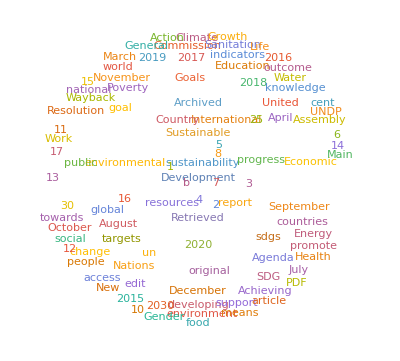

```mathematica
WordCloud[sdgWiki]
```

You can also import specific elements:

```mathematica
Import["https://en.wikipedia.org/wiki/Sustainable_Development_Goals","Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

```mathematica
Import["https://en.wikipedia.org/wiki/Sustainable_Development_Goals", "Images"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Import["https://en.wikipedia.org/wiki/Sustainable_Development_Goals", "Hyperlinks"]
```

{https://en.wikipedia.org/wiki/SDG_(disambiguation),https://en.wikipedia.org/wiki/File:Sustainable_Development_Goals_logo.svg,https://en.wikipedia.org/wiki/Mission_statement,1573,https://wikimediafoundation.org/,https://www.mediawiki.org/}
 |  |  |  |

Note that for Wikipedia articles, the function WikipediaData also allows to import the plain text of the article or specific properties.

## Useful links

Fast Introduction for Programmers

Videos "Real-World Entities" from the Fast Introduction for Programmers

Computation with Structure Dataset

Wolfram Data Repository